```mathematica
Quit[]
```

```mathematica
Get["DdimPackage.wl"]
```

Get::noopen: Cannot open YoungSymm`.

Needs::nocont: Context YoungSymm` was not created when Needs was evaluated.

```mathematica
Get["/Users/gangchen/Documents/GitHub/FaRe2/Amplitude/1-loop_HEFT_amplitude_result.wl"]
```

parametrise picks a frame (here I am considering the ϵ_k^+ helicity polarisation):

```mathematica
parametrise[exp_]:=ReplaceRepeated[exp,{DotProduct[Momentum[x_],Momentum[y_]]:>x.DiagonalMatrix[{1,-1,-1,-1}].y,DotProduct[EpsilonPol[k],Momentum[y_]]:>ϵk.DiagonalMatrix[{1,-1,-1,-1}].y}]/.{u1->{1,0,0,0},u2->{γ,V γ,0,0},k->{ω,ω Cos[ϕ] Sin[θ],ω Sin[θ] Sin[ϕ],ω Cos[θ]},b->{0,0,B,0},v->{0,0,0,4 B √(-1+γ^2)},ϵk->{(Sin[θ] (ⅈ Abs[Cos[θ]] Cos[ϕ]+Sin[ϕ]))/(1-Cos[ϕ]^2 Sin[θ]^2),(ⅈ Abs[Cos[θ]]+Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(1-Cos[ϕ]^2 Sin[θ]^2),1,0}}
```

```mathematica
(*{k.DiagonalMatrix[{1,-1,-1,-1}].{ϵk0,ϵk1,ϵk2,ϵk3},{ϵk0,ϵk1,ϵk2,ϵk3}.DiagonalMatrix[{1,-1,-1,-1}].{ϵk0,ϵk1,ϵk2,ϵk3}}/.{u1->{1,0,0,0},u2->{γ,γ v,0,0},k->ω{1,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},b->{0,0,b,0},v->{0,0,0,4 b Sqrt[γ^2-1]}}
Solve[%==0,{ϵk0,ϵk1}][[1]]
%/.θ->0/.{ϵk3->0,ϵk2->1}*)
```

### TestA

```mathematica
amp5=(amp5m13m22)/. {lw1->0,dIR->0}/. replaceDivergences/. replaceTree/. replacer[]/. replacelq[]/. replacely[]/. replacelw2[]/. replaceTriangleIntegrals/. replacec1/. replacec2;
```

```mathematica
(*amp5=amp5m13m22/. replaceDivergences/. amp5TreeLevel->0/. replacer[]/. replacelq[]/. replacely[]/. replacelw2[]/.replaceTriangleIntegrals/.replacec1/.replacec2;*)
```

```mathematica
%//.{F1->FTrace[Momentum[q1],{FieldStr[k]},Momentum[v1]],F2->FTrace[Momentum[q2],{FieldStr[k]},Momentum[v2]],F3->FTrace[Momentum[v1],{FieldStr[k]},Momentum[v2]]};
%//.FTrace[a_,{FieldStr[k_]},b_]:>DotProduct[a,Momentum[k]]DotProduct[b,EpsilonPol[k]]-DotProduct[b,Momentum[k]]DotProduct[a,EpsilonPol[k]];
%//.{qq1->-DotProduct[Momentum[q1],Momentum[q1]],qq2->-DotProduct[Momentum[q2],Momentum[q2]],w1->DotProduct[Momentum[v1],Momentum[k]],w2->DotProduct[Momentum[v2],Momentum[k]],y->DotProduct[Momentum[v1],Momentum[v2]]};
%//.{v2->u2,v1->u1,y->γ};
%/.{Momentum[q2]->Momentum[k]-Momentum[q1]};
Sqrt[(γ^2-1)]%//.{Momentum[q1]->z1 Momentum[u1]+z2 Momentum[u2]+zb Momentum[bt]+zv Momentum[vt]};
%//.{DotProduct[Momentum[u1],Momentum[u2]]->γ,DotProduct[Momentum[bt],Momentum[bt]]->-1,DotProduct[Momentum[vt],Momentum[vt]]->-1,DotProduct[Momentum[u1],Momentum[u1]]->1,DotProduct[Momentum[u2],Momentum[u2]]->1};
%//.{DotProduct[Momentum[u1],Momentum[bt]]->0,DotProduct[Momentum[u2],Momentum[bt]]->0,DotProduct[Momentum[u1],Momentum[vt]]->0,DotProduct[Momentum[u2],Momentum[vt]]->0,DotProduct[Momentum[vt],Momentum[bt]]->0};
%/.{z1->(DotProduct[Momentum[u2],Momentum[k]] γ)/(-1+γ^2),z2->-DotProduct[Momentum[u2],Momentum[k]]/(-1+γ^2)};
%/.{Momentum[bt]->Momentum[b]/Sqrt[-DotProduct[Momentum[b],Momentum[b]]],Momentum[vt]->Momentum[v]/(4Sqrt[-DotProduct[Momentum[b],Momentum[b]](γ^2-1)])}/.γ->DotProduct[Momentum[u1],Momentum[u2]]//parametrise;
%/.{V->(√(-1+γ^2))/γ,B->b};
(*%//Reduce`FreeVariables*)
%/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->2(*ω->3*)};
amp1=%+ReplaceAll[%,zv->-zv];
(*%//Series[#,zv->Infinity]&
%%//Series[#,{zb,Infinity,0}]&*)
```

```mathematica
amp1=amp1//Expand;
```

```mathematica
Monitor[amp1a=Sum[amp1[[ii]]//Simplify,{ii,Length@amp1}];,ii]
```

### TestB

```mathematica
amp5=I(amp5m13m22)/. {lw1->0,dIR->0}/. replaceDivergences/. replaceTree/. replacer[]/. replacelq[]/. replacely[]/. replacelw2[]/. replaceTriangleIntegrals/. replacec1/. replacec2;
%//.{F1->FTrace[Momentum[q1],{FieldStr[k]},Momentum[v1]],F2->FTrace[Momentum[q2],{FieldStr[k]},Momentum[v2]],F3->FTrace[Momentum[v1],{FieldStr[k]},Momentum[v2]]};
%//.FTrace[a_,{FieldStr[k_]},b_]:>DotProduct[a,Momentum[k]]DotProduct[b,EpsilonPol[k]]-DotProduct[b,Momentum[k]]DotProduct[a,EpsilonPol[k]];
%//.{qq1->-DotProduct[Momentum[q1],Momentum[q1]],qq2->-DotProduct[Momentum[q2],Momentum[q2]],w1->DotProduct[Momentum[v1],Momentum[k]],w2->DotProduct[Momentum[v2],Momentum[k]],y->DotProduct[Momentum[v1],Momentum[v2]]};
%//.{v2->u2,v1->u1,y->γ};
%/.{Momentum[q2]->Momentum[k]-Momentum[q1]};
Sqrt[(γ^2-1)]%//.{Momentum[q1]->z1 Momentum[u1]+z2 Momentum[u2]+zb Momentum[bt]+zv Momentum[vt]};
%//.{DotProduct[Momentum[u1],Momentum[u2]]->γ,DotProduct[Momentum[bt],Momentum[bt]]->-1,DotProduct[Momentum[vt],Momentum[vt]]->-1,DotProduct[Momentum[u1],Momentum[u1]]->1,DotProduct[Momentum[u2],Momentum[u2]]->1};
%//.{DotProduct[Momentum[u1],Momentum[bt]]->0,DotProduct[Momentum[u2],Momentum[bt]]->0,DotProduct[Momentum[u1],Momentum[vt]]->0,DotProduct[Momentum[u2],Momentum[vt]]->0,DotProduct[Momentum[vt],Momentum[bt]]->0};
%/.{z1->(DotProduct[Momentum[u2],Momentum[k]] γ)/(-1+γ^2),z2->-DotProduct[Momentum[u2],Momentum[k]]/(-1+γ^2)};
%/.{Momentum[bt]->Momentum[b]/Sqrt[-DotProduct[Momentum[b],Momentum[b]]],Momentum[vt]->Momentum[v]/(4Sqrt[-DotProduct[Momentum[b],Momentum[b]](γ^2-1)])}/.γ->DotProduct[Momentum[u1],Momentum[u2]]//parametrise;
%/.{V->(√(-1+γ^2))/γ,B->b};
(*%//Reduce`FreeVariables*)
%/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->2(*ω->3*)};
amp1b=%+ReplaceAll[%,zv->-zv];
```

```mathematica
amp1b=amp1b//Expand;
```

```mathematica
Monitor[amp1b=Sum[amp1b[[ii]]//Simplify,{ii,Length@amp1b}];,ii]
```

```mathematica
amp1//Length
```

3611

```mathematica
amp2w0a=Series[amp1a,{ω,0,0}]//Normal;
ta=amp2w0a//Simplify//Expand;
```

```mathematica
amp2w0b=Series[amp1b,{ω,0,0}]//Normal;
tb=amp2w0b//Simplify//Expand;
```

```mathematica
I*ta- tb//Simplify
```

0

### Continue

```mathematica
Monitor[amp2=Sum[amp1[[ii]]//Simplify,{ii,Length@amp1}];,ii]
```

```mathematica
(List@@@(Denominator/@(List@@amp2)))//Flatten//Union
%/.{zb->zv}
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[amp2].

Flatten[amp2]

Flatten[amp2]

```mathematica
Series[amp2,{zv,∞,1}]
```

(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 ω zv)+O[1/zv]^2

```mathematica
Series[(171 (4+ⅈ √3) zb)/(4096 √2 √(zb^2+zv^2)),{zv,∞,+1}]//Normal//Simplify
```

(171 (4+ⅈ √3) zb)/(4096 √2 zv)

```mathematica
(9 (76 √2 zb+19 ⅈ √6 zb))/(8192 ω zv)//Simplify
```

(171 (4+ⅈ √3) zb)/(4096 √2 zv ω)

```mathematica
(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 ω zv)
```

```mathematica
Series[(amp2-(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 ω (zv+ ω))),{zv,∞,+1}]
```

O[1/zv]^2

```mathematica
amp2[[1234]]
```

(222490071 √(3/2) zb^4 zv^9 ω^2)/(1024 π (3 zb^2+3 zv^2+4 ω^2) (3 zb^2+3 zv^2-3 √2 zb ω+3 √2 zv ω+4 ω^2) (3 zb^2+3 zv^2-3 √2 zb ω+3 √2 zv ω+7 ω^2)^3 (3 zb^2+6 zb zv+3 zv^2+8 ω^2)^3)

```mathematica
amp2w0=Series[amp2,{ω,0,0}]//Normal;
```

```mathematica
amp2w0=amp2w0//Simplify//Expand
```

```mathematica
ta=(9 ⅈ √3 zb^2)/(2048 (zb^2+zv^2)^(3/2))+(9 ⅈ √3 zv^2)/(2048 (zb^2+zv^2)^(3/2))+((21/128-(35 ⅈ)/512) zb)/(√2 (zb^2+zv^2))-((35/128-(63 ⅈ)/512) zb)/(√6 (zb^2+zv^2))+(123 √(3/2) zb)/(512 π (zb^2+zv^2))+(3 ⅈ zb)/(128 √2 π (zb^2+zv^2))+(171 ⅈ √(3/2) zb^3)/(4096 (zb^2+zv^2)^(3/2) ω)+(171 zb^3)/(1024 √2 (zb^2+zv^2)^(3/2) ω)+(171 ⅈ √(3/2) zb zv^2)/(4096 (zb^2+zv^2)^(3/2) ω)+(171 zb zv^2)/(1024 √2 (zb^2+zv^2)^(3/2) ω)+(91 ⅈ zb Log[4])/(384 √2 π (zb^2+zv^2))+(133 zb Log[4])/(512 √6 π (zb^2+zv^2))-(21 zb Log[2+√3])/(64 √2 π (zb^2+zv^2))-(49 ⅈ zb Log[2+√3])/(64 √6 π (zb^2+zv^2));
```

```mathematica
tb=(9 √3 zb^2)/(1024 (zb^2+zv^2)^(3/2))+(9 √3 zv^2)/(1024 (zb^2+zv^2)^(3/2))-((35/256-(21 ⅈ)/64) zb)/(√2 (zb^2+zv^2))+((63/256-(35 ⅈ)/64) zb)/(√6 (zb^2+zv^2))-(123 ⅈ √(3/2) zb)/(256 π (zb^2+zv^2))-(3 zb)/(64 √2 π (zb^2+zv^2))+(171 √(3/2) zb^3)/(2048 (zb^2+zv^2)^(3/2) ω)+(171 ⅈ zb^3)/(512 √2 (zb^2+zv^2)^(3/2) ω)+(171 √(3/2) zb zv^2)/(2048 (zb^2+zv^2)^(3/2) ω)+(171 ⅈ zb zv^2)/(512 √2 (zb^2+zv^2)^(3/2) ω)-(91 zb Log[4])/(192 √2 π (zb^2+zv^2))-(133 ⅈ zb Log[4])/(256 √6 π (zb^2+zv^2))+(21 ⅈ zb Log[2+√3])/(32 √2 π (zb^2+zv^2))+(49 zb Log[2+√3])/(32 √6 π (zb^2+zv^2));
```

```mathematica
2ta-I tb//Simplify
```

(zb (π (513 zb^2+513 zv^2+56 (9-5 √3) √(zb^2+zv^2) ω)+8 ⅈ √(zb^2+zv^2) ω (9+91 Log[4]-98 √3 Log[2+√3])))/(768 √2 π (zb^2+zv^2)^(3/2) ω)

```mathematica
amp2w0
```

(9 ⅈ √3 zb^2)/(2048 (zb^2+zv^2)^(3/2))+(9 ⅈ √3 zv^2)/(2048 (zb^2+zv^2)^(3/2))+((21/128-(35 ⅈ)/512) zb)/(√2 (zb^2+zv^2))-((35/128-(63 ⅈ)/512) zb)/(√6 (zb^2+zv^2))+(123 √(3/2) zb)/(512 π (zb^2+zv^2))+(3 ⅈ zb)/(128 √2 π (zb^2+zv^2))+(171 ⅈ √(3/2) zb^3)/(4096 (zb^2+zv^2)^(3/2) ω)+(171 zb^3)/(1024 √2 (zb^2+zv^2)^(3/2) ω)+(171 ⅈ √(3/2) zb zv^2)/(4096 (zb^2+zv^2)^(3/2) ω)+(171 zb zv^2)/(1024 √2 (zb^2+zv^2)^(3/2) ω)+(91 ⅈ zb Log[4])/(384 √2 π (zb^2+zv^2))+(133 zb Log[4])/(512 √6 π (zb^2+zv^2))-(21 zb Log[2+√3])/(64 √2 π (zb^2+zv^2))-(49 ⅈ zb Log[2+√3])/(64 √6 π (zb^2+zv^2))

```mathematica
Series[amp2w0,{zv,∞,+1}]//Normal
```

(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 zv ω)

### RegularizedNewHighw

```mathematica
amp2w0new1=(171 ⅈ √(3/2) zb^3)/(4096 (zb^2+zv^2)^(3/2) ω)+(171 zb^3)/(1024 √2 (zb^2+zv^2)^(3/2) ω)+(171 ⅈ √(3/2) zb zv^2)/(4096 (zb^2+zv^2)^(3/2) ω)+(171 zb zv^2)/(1024 √2 (zb^2+zv^2)^(3/2) ω)//Simplify
```

(171 (4+ⅈ √3) zb)/(4096 √2 √(zb^2+zv^2) ω)

```mathematica
amp2w0new2=(9 ⅈ √3 zb^2)/(2048 (zb^2+zv^2)^(3/2))+(9 ⅈ √3 zv^2)/(2048 (zb^2+zv^2)^(3/2))//Simplify
```

(9 ⅈ √3)/(2048 √(zb^2+zv^2))

```mathematica
Assuming[b>0,FourierTransform[(171 (4+ⅈ √3) zb)/(4096 √2 √(zb^2+(zv+ω)^2)),zb,b]//PowerExpand]
```

(171 ⅈ (4+ⅈ √3) (zv+ω) BesselK[1,b (zv+ω)])/(4096 √π)

```mathematica
Integrate[(171 ⅈ (4+ⅈ √3) (zv+ω) BesselK[1,b (zv+ω)])/(4096 √π),zv]
```

-(171 (-4 ⅈ+√3) (zv+ω)^2 MeijerG[{{0},{}},{{-1/2,1/2},{-1}},1/2 b (zv+ω),1/2])/(16384 √π)

```mathematica
Limit[MeijerG[{{0},{}},{{-1/2,1/2},{-1}},1/2 b (zv+ω),1/2],zv->∞]
```

lim_(zv→∞) MeijerG[{{0},{}},{{-1/2,1/2},{-1}},1/2 b (zv+ω),1/2]

```mathematica
Assuming[b>0,FourierTransform[(9 ⅈ √3)/(2048 √(zb^2+zv^2+ω^2)),zb,b]//PowerExpand]
```

(9 ⅈ √(3/(2 π)) BesselK[0,b √(zv^2+ω^2)])/1024

```mathematica
NIntegrate[BesselK[0, √(zv^2+0.00000001^2)],{zv,0,∞}]
```

1.5708

```mathematica
NIntegrate[(171 ⅈ (4+ⅈ √3) √(zv^2+0.000001) BesselK[1, √(zv^2+0.000001)])/(4096 √π),{zv,0,∞}]
```

-0.0640828+0.147993 ⅈ

```mathematica
amp2w0new3=((21/128-(35 ⅈ)/512) zb)/(√2 (zb^2+zv^2))-((35/128-(63 ⅈ)/512) zb)/(√6 (zb^2+zv^2))+(123 √(3/2) zb)/(512 π (zb^2+zv^2))+(3 ⅈ zb)/(128 √2 π (zb^2+zv^2))+(91 ⅈ zb Log[4])/(384 √2 π (zb^2+zv^2))+(133 zb Log[4])/(512 √6 π (zb^2+zv^2))-(21 zb Log[2+√3])/(64 √2 π (zb^2+zv^2))-(49 ⅈ zb Log[2+√3])/(64 √6 π (zb^2+zv^2))//Simplify
```

1/(1536 √2 π (zb^2+zv^2))zb (36 ⅈ+369 √3+7 ⅈ ((-15-36 ⅈ)+(9+20 ⅈ) √3) π+7 (52 ⅈ+19 √3) Log[4]-504 Log[2+√3]-392 ⅈ √3 Log[2+√3])

```mathematica
amp2w0
```

(9 ⅈ √3 zb^2)/(2048 (zb^2+zv^2)^(3/2))+(9 ⅈ √3 zv^2)/(2048 (zb^2+zv^2)^(3/2))+((21/128-(35 ⅈ)/512) zb)/(√2 (zb^2+zv^2))-((35/128-(63 ⅈ)/512) zb)/(√6 (zb^2+zv^2))+(123 √(3/2) zb)/(512 π (zb^2+zv^2))+(3 ⅈ zb)/(128 √2 π (zb^2+zv^2))+(171 ⅈ √(3/2) zb^3)/(4096 (zb^2+zv^2)^(3/2) ω)+(171 zb^3)/(1024 √2 (zb^2+zv^2)^(3/2) ω)+(171 ⅈ √(3/2) zb zv^2)/(4096 (zb^2+zv^2)^(3/2) ω)+(171 zb zv^2)/(1024 √2 (zb^2+zv^2)^(3/2) ω)+(91 ⅈ zb Log[4])/(384 √2 π (zb^2+zv^2))+(133 zb Log[4])/(512 √6 π (zb^2+zv^2))-(21 zb Log[2+√3])/(64 √2 π (zb^2+zv^2))-(49 ⅈ zb Log[2+√3])/(64 √6 π (zb^2+zv^2))

```mathematica
-amp2w0new1-amp2w0new2-amp2w0new3
```

-(9 ⅈ √3)/(2048 √(zb^2+zv^2))-(171 (4+ⅈ √3) zb)/(4096 √2 √(zb^2+zv^2) ω)-(zb (36 ⅈ+369 √3+7 ⅈ ((-15-36 ⅈ)+(9+20 ⅈ) √3) π+7 (52 ⅈ+19 √3) Log[4]-504 Log[2+√3]-392 ⅈ √3 Log[2+√3]))/(1536 √2 π (zb^2+zv^2))

```mathematica
amp2w0-amp2w0new1-amp2w0new2-amp2w0new3//Simplify
```

0

```mathematica
(*amp2w0reg=amp2w0/.(zb^2+zv^2):>(zb^2+zv^2+ω^2);*)
```

```mathematica
amp2w0reg=amp2w0new1+amp2w0new2+amp2w0new3/.(zb^2+zv^2):>(zb^2+zv^2+ω^2);
```

```mathematica
amp2w0reg//Simplify
```

1/24576((108 ⅈ √3)/(√(zb^2+zv^2+ω^2))+(513 √2 (4+ⅈ √3) zb)/(ω √(zb^2+zv^2+ω^2))+1/(π (zb^2+zv^2+ω^2))8 √2 zb (36 ⅈ+369 √3+7 ⅈ ((-15-36 ⅈ)+(9+20 ⅈ) √3) π+7 (52 ⅈ+19 √3) Log[4]-504 Log[2+√3]-392 ⅈ √3 Log[2+√3]))

```mathematica
ampReg=(amp2-amp2w0reg)* Exp[-I zb-0.001Abs[zb]];
```

```mathematica
(*ampUnReg=(amp2)* Exp[-I zb-0.001Abs[zb]];
ampNumUnReg=ampUnReg/.ω->1//Expand;*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["waveformIntgrand.txt",{ampReg}]
```

/Users/gangchen/Documents/GitHub/FaRe2

waveformIntgrand.txt

```mathematica
SetDirectory[NotebookDirectory[]]
ampReg=Import["waveformIntgrand.txt"]//ToExpression;
```

/Users/gangchen/Documents/GitHub/FaRe2

### Test

```mathematica
ampNumReg=N[ampReg/.ω->0.4,50];
```

```mathematica
Monitor[wflist11=Table[NIntegrate[ampNumReg,{zv,0,ii},{zb,-π*ii,+π*ii},Method->"LocalAdaptive"],{ii,1,10}];,ii]
```

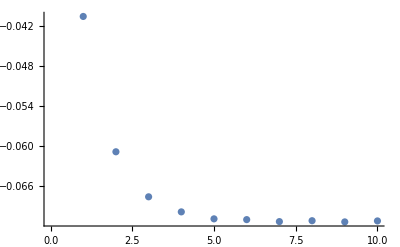

```mathematica
ListPlot[{Im/@Join[wflist11,{}]}]
```

```mathematica
ampNumReg=N[ampReg/.ω->1.2,50];
```

```mathematica
Monitor[wflist11=Table[NIntegrate[ampNumReg,{zv,0,ii},{zb,-π*ii,+π*ii},Method->"LocalAdaptive"],{ii,1,10}];,ii]
```

```mathematica
Monitor[wflist12=Table[NIntegrate[ampNumReg,{zv,0,ii},{zb,-π*ii,+π*ii},Method->"LocalAdaptive"],{ii,11,20}];,ii]
Monitor[wflist13=Table[NIntegrate[ampNumReg,{zv,0,ii},{zb,-π*ii,+π*ii},Method->"LocalAdaptive"],{ii,21,30}];,ii]
```

$Aborted

```mathematica
Monitor[wflist14=Table[NIntegrate[ampNumReg,{zv,0,ii},{zb,-π*ii,+π*ii},Method->"LocalAdaptive"],{ii,31,38}];,ii]
```

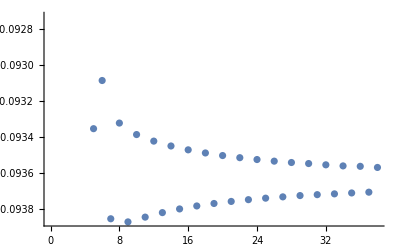

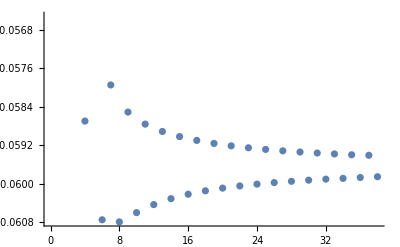

```mathematica
ListPlot[{Im/@Join[wflist11,wflist12,wflist13,wflist14]}]
ListPlot[{Re/@Join[wflist11,wflist12,wflist13,wflist14]}]
```

```mathematica
Monitor[wflist11=Table[NIntegrate[ampNumReg,{zv,0,ii},{zb,-π*ii,+π*ii},Method->"LocalAdaptive"],{ii,1,30}];,ii]
```

```mathematica
Join[wflist11,wflist12,wflist13]
```

{-0.0140969-0.0472897 ⅈ,-0.0467814-0.0771574 ⅈ,-0.0473346-0.0884569 ⅈ,-0.0586947-0.0913928 ⅈ,-0.0559963-0.0933549 ⅈ,-0.0607456-0.0930877 ⅈ,-0.0579442-0.0938547 ⅈ,-0.0607896-0.0933237 ⅈ,-0.0585076-0.093872 ⅈ,-0.0605965-0.0933875 ⅈ,-0.0587581-0.0938455 ⅈ,-0.0604303-0.0934239 ⅈ,-0.0589103-0.0938205 ⅈ,-0.060307-0.0934509 ⅈ,-0.059017-0.0938002 ⅈ,-0.0602149-0.0934723 ⅈ,-0.0590969-0.0937836 ⅈ,-0.0601439-0.0934896 ⅈ,-0.0591591-0.0937699 ⅈ,-0.0600878-0.0935039 ⅈ,-0.059209-0.0937585 ⅈ,-0.0600422-0.0935158 ⅈ,-0.0592497-0.0937487 ⅈ,-0.0600044-0.0935261 ⅈ,-0.0592837-0.0937404 ⅈ,-0.0599728-0.0935351 ⅈ,-0.0593126-0.0937331 ⅈ,-0.0599461-0.0935426 ⅈ,-0.0593375-0.093726 ⅈ,-0.0599225-0.0935483 ⅈ}

```mathematica
wflist11
```

{0.+0.0243614 ⅈ,5.28138×10^-10+0.0634179 ⅈ,1.70539×10^-10+0.105028 ⅈ,-6.66134×10^-16+0.147449 ⅈ,0.+0.19022 ⅈ,8.88178×10^-16+0.233172 ⅈ,0.+0.27623 ⅈ,-1.40791×10^-8+0.319354 ⅈ,-3.55271×10^-15+0.362523 ⅈ,-1.86926×10^-11+0.405723 ⅈ,8.44565×10^-10+0.448946 ⅈ,-3.55271×10^-15+0.492186 ⅈ,1.91029×10^-7+0.53544 ⅈ,3.55271×10^-15+0.578704 ⅈ,-2.12807×10^-8+0.621976 ⅈ,-1.06581×10^-14+0.665256 ⅈ,6.25567×10^-8+0.70854 ⅈ,-1.42109×10^-14+0.75183 ⅈ,2.13163×10^-14+0.795123 ⅈ,1.11953×10^-7+0.83842 ⅈ,0.+0.88172 ⅈ,7.10543×10^-15+0.925022 ⅈ,-1.76223×10^-9+0.968326 ⅈ,0.+1.01163 ⅈ,-2.84217×10^-14+1.05494 ⅈ,0.+1.09825 ⅈ,-2.84217×10^-14+1.14156 ⅈ,1.42109×10^-14+1.18487 ⅈ,-4.47558×10^-9+1.22818 ⅈ,-5.68434×10^-14+1.2715 ⅈ}

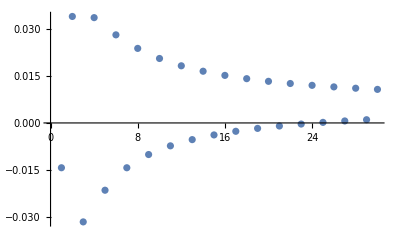

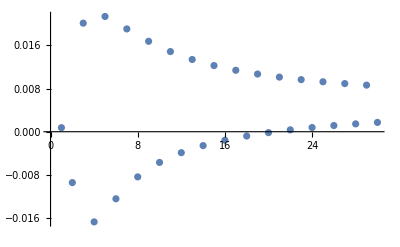

```mathematica
ListPlot[{Im/@wflist11}]
ListPlot[{Re/@wflist11}]
```

### Plot WaveForm

```mathematica
Monitor[wflist=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,20},{zb,-π*20,+π*20},Method->"LocalAdaptive"],{ii,0.8,2.2,0.1}];,ii]
```

```mathematica
wfIm=Table[{0.7+0.1*ii,Im[wflist[[ii]]]},{ii,Length@wflist}];
wfRe=Table[{0.7+0.1*ii,Re[wflist[[ii]]]},{ii,Length@wflist}];
```

```mathematica
Monitor[wflist2=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,30},{zb,-π*30,+π*30},Method->"LocalAdaptive"],{ii,0.8,2.2,0.1}];,ii]
```

```mathematica
wfIm2=Table[{0.7+0.1*ii,Im[wflist2[[ii]]]},{ii,Length@wflist2}];
wfRe2=Table[{0.7+0.1*ii,Re[wflist2[[ii]]]},{ii,Length@wflist2}];
```

```mathematica
Monitor[wflist3=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,20},{zb,-π*20,+π*20},Method->"LocalAdaptive"],{ii,2.3,4.2,0.1}];,ii]
```

```mathematica
wfIm3=Table[{2.2+0.1*ii,Im[wflist3[[ii]]]},{ii,Length@wflist3}];
wfRe3=Table[{2.2+0.1*ii,Re[wflist3[[ii]]]},{ii,Length@wflist3}];
```

```mathematica
Monitor[wflist5=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,20},{zb,-π*20,+π*20},Method->"LocalAdaptive"],{ii,4.3,6.2,0.1}];,ii]
```

```mathematica
wfIm5=Table[{4.2+0.1*ii,Im[wflist5[[ii]]]},{ii,Length@wflist5}];
wfRe5=Table[{4.2+0.1*ii,Re[wflist5[[ii]]]},{ii,Length@wflist5}];
```

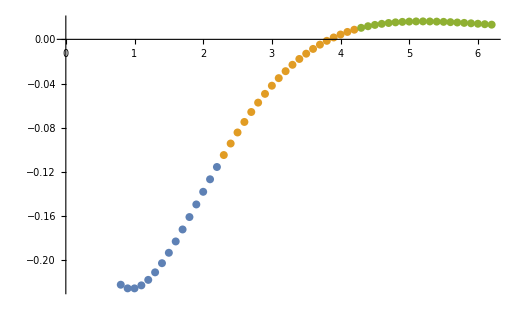

```mathematica
ListPlot[{wfIm,wfIm3,wfIm5}]
```

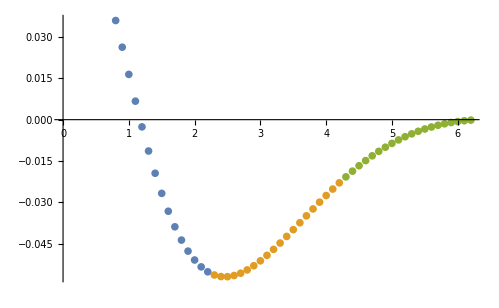

```mathematica
ListPlot[{wfRe,wfRe3,wfRe5}]
```

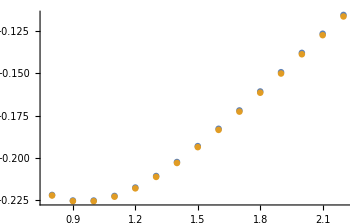

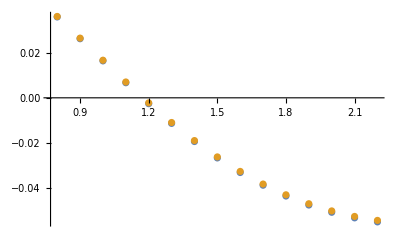

```mathematica
ListPlot[{wfIm,wfIm2}]
ListPlot[{wfRe,wfRe2}]
```

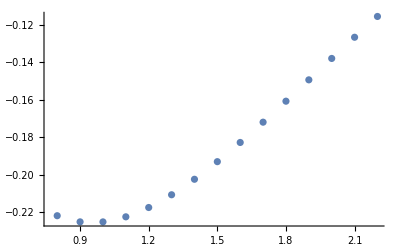

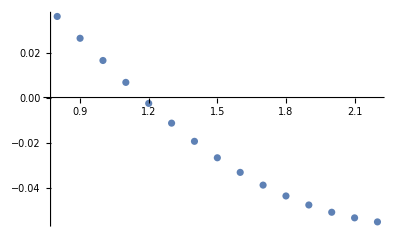

```mathematica
ListPlot[wfRe]
```

### Plot WaveFormFull

#### r=10

```mathematica
ampNumUnReg=ampReg/.ω->0.2;
NIntegrate[ampNumUnReg,{zv,0,10},{zb,-π*10,+π*10},Method->"LocalAdaptive"]
```

0.0276195-0.0411788 ⅈ

```mathematica
Monitor[wflist101=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,10},{zb,-π*10,+π*10},Method->"LocalAdaptive"],{ii,0.2,6.2,0.1}];,ii]
```

```mathematica
wfIm101=Table[{0.1+0.1*ii,Im[wflist101[[ii]]]},{ii,Length@wflist101}];
wfRe101=Table[{0.1+0.1*ii,Re[wflist101[[ii]]]},{ii,Length@wflist101}];
```

#### r=20

```mathematica
Monitor[wflist=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,20},{zb,-π*20,+π*20},Method->"LocalAdaptive"],{ii,0.8,2.2,0.1}];,ii]
```

```mathematica
wfIm=Table[{0.7+0.1*ii,Im[wflist[[ii]]]},{ii,Length@wflist}];
wfRe=Table[{0.7+0.1*ii,Re[wflist[[ii]]]},{ii,Length@wflist}];
```

```mathematica
Monitor[wflist3=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,20},{zb,-π*20,+π*20},Method->"LocalAdaptive"],{ii,2.3,4.2,0.1}];,ii]
```

```mathematica
wfIm3=Table[{2.2+0.1*ii,Im[wflist3[[ii]]]},{ii,Length@wflist3}];
wfRe3=Table[{2.2+0.1*ii,Re[wflist3[[ii]]]},{ii,Length@wflist3}];
```

```mathematica
Monitor[wflist5=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,20},{zb,-π*20,+π*20},Method->"LocalAdaptive"],{ii,4.3,6.2,0.1}];,ii]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zb near {zv,zb} = {4.73533,4.73568}. NIntegrate obtained 4.22645×10^-11-4.16163×10^-11 ⅈ and 5.36168×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zv near {zv,zb} = {4.73531,4.73574}. NIntegrate obtained 1.20125×10^-10+1.08622×10^-11 ⅈ and 4.76681×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zv near {zv,zb} = {4.73533,4.73574}. NIntegrate obtained -2.5835×10^-11+2.23588×10^-10 ⅈ and 5.28181×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
wfIm5=Table[{4.2+0.1*ii,Im[wflist5[[ii]]]},{ii,Length@wflist5}];
wfRe5=Table[{4.2+0.1*ii,Re[wflist5[[ii]]]},{ii,Length@wflist5}];
```

#### r=30

```mathematica
Monitor[wflist2=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,30},{zb,-π*30,+π*30},Method->"LocalAdaptive"],{ii,0.8,2.2,0.1}];,ii]
```

```mathematica
wfIm2=Table[{0.7+0.1*ii,Im[wflist2[[ii]]]},{ii,Length@wflist2}];
wfRe2=Table[{0.7+0.1*ii,Re[wflist2[[ii]]]},{ii,Length@wflist2}];
```

```mathematica
Monitor[wflist4=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,30},{zb,-π*30,+π*30},Method->"LocalAdaptive"],{ii,2.3,4.2,0.1}];,ii]
```

```mathematica
wfIm4=Table[{2.2+0.1*ii,Im[wflist4[[ii]]]},{ii,Length@wflist4}];
wfRe4=Table[{2.2+0.1*ii,Re[wflist4[[ii]]]},{ii,Length@wflist4}];
```

```mathematica
Monitor[wflist6=Table[ampNumUnReg=ampReg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,30},{zb,-π*30,+π*30},Method->"LocalAdaptive"],{ii,4.3,6.2,0.1}];,ii]
```

```mathematica
wfIm6=Table[{4.2+0.1*ii,Im[wflist6[[ii]]]},{ii,Length@wflist6}];
wfRe6=Table[{4.2+0.1*ii,Re[wflist6[[ii]]]},{ii,Length@wflist6}];
```

#### Plot

```mathematica
wfIm101
```

```mathematica
wfIm101={{0.2,-0.041178803313860604},{0.30000000000000004,-0.057694713102705734},{0.4,-0.07121369164308763},{0.5,-0.08179615920903273},{0.6,-0.089638660991982},{0.7000000000000001,-0.09498305486743287},{0.8,-0.09809135771990686},{0.9,-0.0992300408551607},{1.,-0.09866081977541288},{1.1,-0.09663456593025145},{1.2000000000000002,-0.09338748723299024},{1.3000000000000003,-0.08913877076641802},{1.4000000000000001,-0.08408935190673394},{1.5000000000000002,-0.07842138558176658},{1.6,-0.0722983318407412},{1.7000000000000002,-0.06586540603442981},{1.8000000000000003,-0.05925033712420657},{1.9000000000000001,-0.05256429161555393},{2.,-0.04590293552347044},{2.1,-0.03934756773193343},{2.2,-0.03296627637172093},{2.3000000000000003,-0.026815108533791168},{2.4000000000000004,-0.020939208642397726},{2.5000000000000004,-0.015373926476969045},{2.6,-0.010145874999740507},{2.7,-0.005273930117527008},{2.8000000000000003,-0.0007701703431608887},{2.9000000000000004,0.0033592504411714677},{3.0000000000000004,0.007113297717881203},{3.1,0.010495297111371083},{3.2,0.013512290943000733},{3.3000000000000003,0.01617438812225693},{3.4000000000000004,0.018494225657956387},{3.5000000000000004,0.020486466475948026},{3.6,0.022167351385024264},{3.7,0.023554306413280424},{3.8000000000000003,0.024665589866493608},{3.9000000000000004,0.02551999419158396},{4.,0.026136564241442083},{4.1,0.02653438219300228},{4.2,0.026732364748553575},{4.3,0.026749088115952595},{4.3999999999999995,0.026602667528713986},{4.5,0.02631062296533644},{4.6,0.025889795557974576},{4.7,0.025356272160690967},{4.8,0.02472532973266575},{4.9,0.0240113943033712},{5.,0.023228014256733216},{5.1,0.022387845230525272},{5.2,0.0215026450779843},{5.3,0.020583278174377495},{5.4,0.019639728091434504},{5.5,0.018681109000225016},{5.6,0.017715702628817658},{5.7,0.01675097213009284},{5.8,0.015793600583822523},{5.9,0.01484952368182504},{6.,0.013923965058582725},{6.1,0.013021475641291136},{6.2,0.012145970767635988}};
```

```mathematica
wfRe101
```

```mathematica
wfRe101={{0.2,0.02761954650660478},{0.30000000000000004,0.025361407428825863},{0.4,0.01910380305696554},{0.5,0.010363287980401923},{0.6,0.0001958511996073371},{0.7000000000000001,-0.010650908394613684},{0.8,-0.021636345279513792},{0.9,-0.03236698188328979},{1.,-0.0425592478418486},{1.1,-0.052013759242992286},{1.2000000000000002,-0.060596517144299304},{1.3000000000000003,-0.06822465318542373},{1.4000000000000001,-0.0748553004144573},{1.5000000000000002,-0.08047677774781437},{1.6,-0.0851014903427589},{1.7000000000000002,-0.08876021331983877},{1.8000000000000003,-0.0914974130079206},{1.9000000000000001,-0.0933674726007512},{2.,-0.0944315960518046},{2.1,-0.0947553182535243},{2.2,-0.09440647395684941},{2.3000000000000003,-0.09345359426685247},{2.4000000000000004,-0.0919646125482564},{2.5000000000000004,-0.09000586285231434},{2.6,-0.08764130599416928},{2.7,-0.08493194776829643},{2.8000000000000003,-0.08193541868601856},{2.9000000000000004,-0.07870568526889238},{3.0000000000000004,-0.07529287177085806},{3.1,-0.07174316907659897},{3.2,-0.06809882090513215},{3.3000000000000003,-0.06439816199265005},{3.4000000000000004,-0.06067570705522563},{3.5000000000000004,-0.05696227594334553},{3.6,-0.053285142969598055},{3.7,-0.0496682117890077},{3.8000000000000003,-0.046132204137833935},{3.9000000000000004,-0.042694837583145843},{4.,-0.03937106491008428},{4.1,-0.03617323919850738},{4.2,-0.03311133589670741},{4.3,-0.03019314425324025},{4.3999999999999995,-0.027424468793457737},{4.5,-0.02480930946951152},{4.6,-0.022350045279549084},{4.7,-0.020047605056071525},{4.8,-0.017901630486306577},{4.9,-0.015910629531349398},{5.,-0.014072120026900491},{5.1,-0.012382764710443517},{5.2,-0.010838495458951707},{5.3,-0.009434629572643492},{5.4,-0.008165976147500276},{5.5,-0.007026932247222287},{5.6,-0.0060115750155739864},{5.7,-0.00511373950874805},{5.8,-0.004327093235848468},{5.9,-0.0036452019794776663},{6.,-0.003061587535443602},{6.1,-0.002569780687806538},{6.2,-0.0021633670194245794}};
```

```mathematica
wf20=Join[wfIm,wfIm3,wfIm5]
```

```mathematica
wf20=Join[wfRe,wfRe3,wfRe5]
```

```mathematica
wf20Re={{0.7999999999999999,-0.02130264535631328},{0.8999999999999999,-0.03199007140031086},{1.,-0.04213867865329231},{1.1,-0.05154925411729196},{1.2,-0.060087781057678744},{1.3,-0.06767132181070022},{1.4,-0.07425709719027473},{1.5,-0.07983342350423676},{1.6,-0.08441269158193748},{1.7,-0.08802570435397096},{1.8,-0.09071693227494106},{1.9000000000000001,-0.09254077535596109},{2.,-0.09355845738865204},{2.1,-0.09383551248044936},{2.2,-0.09343980277884038},{2.3000000000000003,-0.09243987216248947},{2.4000000000000004,-0.09090366692368979},{2.5,-0.0888975398994522},{2.6,-0.08648546984021781},{2.7,-0.08372848150337889},{2.8000000000000003,-0.0806842230353438},{2.9000000000000004,-0.07740668128423395},{3.,-0.07394600087515193},{3.1,-0.07034839224317517},{3.2,-0.06665612186230847},{3.3000000000000003,-0.06290754587531815},{3.4000000000000004,-0.0591372003494122},{3.5,-0.05537592892235228},{3.6000000000000005,-0.051651028838184544},{3.7,-0.04798642713430538},{3.8000000000000003,-0.04440286589641183},{3.9000000000000004,-0.04091809889878039},{4.,-0.03754709195469987},{4.1000000000000005,-0.034302227441459165},{4.2,-0.031193506016972856},{4.3,-0.028228744352600567},{4.4,-0.025413772602645136},{4.5,-0.02275261811904762},{4.6000000000000005,-0.020247687619128645},{4.7,-0.017899937893154007},{4.800000000000001,-0.015709039706713678},{4.9,-0.013673530364925296},{5.,-0.011790957683359339},{5.1000000000000005,-0.010058015204608852},{5.2,-0.008470666468128338},{5.300000000000001,-0.0070242609616231275},{5.4,-0.005713640758988803},{5.5,-0.004533237446532518},{5.6000000000000005,-0.0034771623417178665},{5.7,-0.0025392862010212396},{5.800000000000001,0.001156681626142124},{5.9,-0.000992845253171325},{6.,-0.00037144294221084714},{6.1000000000000005,0.00015732759184057185},{6.2,0.0005998351047421906}};
```

```mathematica
wf20Im={{0.7999999999999999,-0.09816723360582837},{0.8999999999999999,-0.09931637199297451},{1.,-0.09875693766677111},{1.1,-0.09674066723748359},{1.2,-0.09350387544209354},{1.3,-0.08926549357468695},{1.4,-0.08422640596740294},{1.5,-0.07856893949936515},{1.6,-0.07245651612221561},{1.7,-0.06603434490067248},{1.8,-0.05943017242626659},{1.9000000000000001,-0.052755169707343896},{2.,-0.046105019191509757},{2.1,-0.039561024576916314},{2.2,-0.033191282858537216},{2.3000000000000003,-0.027051853484061583},{2.4000000000000004,-0.021187890095541947},{2.5,-0.01563475245085348},{2.6,-0.010419063566301805},{2.7,-0.005559706556028783},{2.8000000000000003,-0.0010687721627667128},{2.9000000000000004,0.003047576713973252},{3.,0.006788293240085615},{3.1,0.010156704077641267},{3.2,0.01315983157519518},{3.3000000000000003,0.0158077796510608},{3.4000000000000004,0.018113177173629903},{3.5,0.020090676846791024},{3.6000000000000005,0.02175651217814294},{3.7,0.023128100265916905},{3.8000000000000003,0.024223692777061125},{3.9000000000000004,0.025062068702344037},{4.,0.025662269655954206},{4.1000000000000005,0.026043367806753193},{4.2,0.026224271968259837},{4.3,0.026223548847043806},{4.4,0.026059306746165273},{4.5,0.025749056915538755},{4.6000000000000005,0.02530963254854973},{4.7,0.024757111985809918},{4.800000000000001,0.02410676457489269},{4.9,0.02337300879656636},{5.,0.022569385253036558},{5.1000000000000005,0.021708542719066626},{5.2,0.0208022323321229},{5.300000000000001,0.01986131236790738},{5.4,0.018895760002382432},{5.5,0.017914688303077554},{5.6000000000000005,0.016926372154409623},{5.7,0.01593827354671983},{5.800000000000001,0.014951544872464579},{5.9,0.013988711746626819},{6.,0.013038410975748314},{6.1000000000000005,0.012110791603476851},{6.2,0.011209580996999051}};
```

```mathematica
wf30=Join[wfIm2,wfIm4,wfIm6]
```

```mathematica
wf30=Join[wfRe2,wfRe4,wfRe6]
```

```mathematica
wf30Re={{0.7999999999999999,-0.021211397517604886},{0.8999999999999999,-0.03187018774105748},{1.,-0.042001302228779014},{1.1,-0.05139896857573041},{1.2,-0.059922999817860235},{1.3,-0.0674920842450959},{1.4,-0.07406335312977239},{1.5,-0.07962534806102903},{1.6,-0.08419034771984059},{1.7,-0.08778894350528228},{1.8,-0.09046570196138709},{1.9000000000000001,-0.09227512851312936},{2.,-0.09327822232998519},{2.1,-0.09354073873772702},{2.2,-0.09313042252649717},{2.3000000000000003,-0.09211584069177008},{2.4000000000000004,-0.09056496789244704},{2.5,-0.08854412756353422},{2.6,-0.08611731362172916},{2.7,-0.0833455443885746},{2.8000000000000003,-0.08028648203953796},{2.9000000000000004,-0.07699410824104855},{3.,-0.07351856997390033},{3.1,-0.06990608144522817},{3.2,-0.066198904117951},{3.3000000000000003,-0.06243540319815377},{3.4000000000000004,-0.058650114754675846},{3.5,-0.05487388183553395},{3.6000000000000005,-0.05113400803165684},{3.7,-0.047454417663838046},{3.8000000000000003,-0.04385585784493515},{3.9000000000000004,-0.04035608161255854},{4.,-0.03697005817403062},{4.1000000000000005,-0.03371017135031786},{4.2,-0.03058642321144043},{4.3,-0.02760663329078579},{4.4,-0.02477663239780892},{4.5,-0.022100450223706797},{4.6000000000000005,-0.01958049508109414},{4.7,-0.017217725939283862},{4.800000000000001,-0.015011815109977846},{4.9,-0.012961301650599971},{5.,-0.011063735468691941},{5.1000000000000005,-0.009315811484012816},{5.2,-0.007713495833401564},{5.300000000000001,-0.006252139041082915},{5.4,-0.00492658531950136},{5.5,-0.00373126857082123},{5.6000000000000005,-0.002660301161106618},{5.7,-0.001707556006477668},{5.800000000000001,-0.0008667387885738492},{5.9,-0.0001314540755410487},{6.,0.0005047368194297814},{6.1000000000000005,0.001048262700407766},{6.2,0.0015054978319556447}};
```

```mathematica
wf30Im={{0.7999999999999999,-0.09821100319318608},{0.8999999999999999,-0.09935528393679507},{1.,-0.09879683257606016},{1.1,-0.09678304119488501},{1.2,-0.09354959644512927},{1.3,-0.08931449135391814},{1.4,-0.08427979452906285},{1.5,-0.07862631752218864},{1.6,-0.072518139727696},{1.7,-0.06610025819093038},{1.8,-0.05950030823990142},{1.9000000000000001,-0.05282958472495313},{2.,-0.04618375052932438},{2.1,-0.03964411677251203},{2.2,-0.03327879415433554},{2.3000000000000003,-0.027143782558979035},{2.4000000000000004,-0.021284297747343865},{2.5,-0.01573568644179933},{2.6,-0.010524559630245555},{2.7,-0.0056698081347282},{2.8000000000000003,-0.0011835218272744212},{2.9000000000000004,0.002928133791874237},{3.,0.006664115211518199},{3.1,0.010027755686251586},{3.2,0.013026069384701678},{3.3000000000000003,0.015669168654664955},{3.4000000000000004,0.01796967233181016},{3.5,0.019942236342144478},{3.6000000000000005,0.02160309475608283},{3.7,0.022969668029202073},{3.8000000000000003,0.024060202461390134},{3.9000000000000004,0.02489348121426246},{4.,0.025488543689514455},{4.1000000000000005,0.02586446226714989},{4.2,0.026040144436757062},{4.3,0.026034162973557207},{4.4,0.025864619799316244},{4.5,0.025549028413625115},{4.6000000000000005,0.02510422196031263},{4.7,0.024546279206454684},{4.800000000000001,0.02389046915939445},{4.9,0.023151210383970357},{5.,0.022342043990904895},{5.1000000000000005,0.021475617702850752},{5.2,0.020563684654376045},{5.300000000000001,0.01961710159203644},{5.4,0.018645846210436412},{5.5,0.017659032355018832},{5.6000000000000005,0.016664934135999135},{5.7,0.01567101384246105},{5.800000000000001,0.01468395425099386},{5.9,0.013709691107699947},{6.,0.01275345089673858},{6.1000000000000005,0.011819788644296177},{6.2,0.010912626149001995}};
```

```mathematica
wf30ImL=Table[{wf30Im[[ii,1]],wf30Im[[ii,2]]*100},{ii,Length@wf30Im}];
wf20ImL=Table[{wf20Im[[ii,1]],wf20Im[[ii,2]]*100},{ii,Length@wf20Im}];
wf10ImL=Table[{wfIm101[[ii,1]],wfIm101[[ii,2]]*100},{ii,Length@wfIm101}];
```

```mathematica
wf30ReL=Table[{wf30Re[[ii,1]],wf30Re[[ii,2]]*100},{ii,Length@wf30Re}];
wf20ReL=Table[{wf20Re[[ii,1]],wf20Re[[ii,2]]*100},{ii,Length@wf20Re}];
wf10ReL=Table[{wfRe101[[ii,1]],wfRe101[[ii,2]]*100},{ii,Length@wfRe101}];
```

```mathematica
wf30ReL
```

{{0.8,-2.12114},{0.9,-3.18702},{1.,-4.20013},{1.1,-5.1399},{1.2,-5.9923},{1.3,-6.74921},{1.4,-7.40634},{1.5,-7.96253},{1.6,-8.41903},{1.7,-8.77889},{1.8,-9.04657},{1.9,-9.22751},{2.,-9.32782},{2.1,-9.35407},{2.2,-9.31304},{2.3,-9.21158},{2.4,-9.0565},{2.5,-8.85441},{2.6,-8.61173},{2.7,-8.33455},{2.8,-8.02865},{2.9,-7.69941},{3.,-7.35186},{3.1,-6.99061},{3.2,-6.61989},{3.3,-6.24354},{3.4,-5.86501},{3.5,-5.48739},{3.6,-5.1134},{3.7,-4.74544},{3.8,-4.38559},{3.9,-4.03561},{4.,-3.69701},{4.1,-3.37102},{4.2,-3.05864},{4.3,-2.76066},{4.4,-2.47766},{4.5,-2.21005},{4.6,-1.95805},{4.7,-1.72177},{4.8,-1.50118},{4.9,-1.29613},{5.,-1.10637},{5.1,-0.931581},{5.2,-0.77135},{5.3,-0.625214},{5.4,-0.492659},{5.5,-0.373127},{5.6,-0.26603},{5.7,-0.170756},{5.8,-0.0866739},{5.9,-0.0131454},{6.,0.0504737},{6.1,0.104826},{6.2,0.15055}}

```mathematica
{0.2,2.76195},{0.3,2.53614},{0.4,1.91038},{0.5,1.03633},{0.6,0.0195851},{0.7,-1.06509},{0.8,-2.16363},{0.9,-3.2367},{1.,-4.25592},{1.1,-5.20138},{1.2,-6.05965},{1.3,-6.82247},{1.4,-7.48553},{1.5,-8.04768},{1.6,-8.51015},{1.7,-8.87602},{1.8,-9.14974},{1.9,-9.33675},{2.,-9.44316},{2.1,-9.47553},{2.2,-9.44065},{2.3,-9.34536},{2.4,-9.19646},{2.5,-9.00059},{2.6,-8.76413},{2.7,-8.49319},{2.8,-8.19354},{2.9,-7.87057},{3.,-7.52929},{3.1,-7.17432},{3.2,-6.80988},{3.3,-6.43982},{3.4,-6.06757},{3.5,-5.69623},{3.6,-5.32851},{3.7,-4.96682},{3.8,-4.61322},{3.9,-4.26948},{4.,-3.93711},{4.1,-3.61732},{4.2,-3.31113},{4.3,-3.01931},{4.4,-2.74245},{4.5,-2.48093},{4.6,-2.235},{4.7,-2.00476},{4.8,-1.79016},{4.9,-1.59106},{5.,-1.40721},{5.1,-1.23828},{5.2,-1.08385},{5.3,-0.943463},{5.4,-0.816598},{5.5,-0.702693},{5.6,-0.601158},{5.7,-0.511374},{5.8,-0.432709},{5.9,-0.36452},{6.,-0.306159},{6.1,-0.256978},{6.2,-0.216337}
```

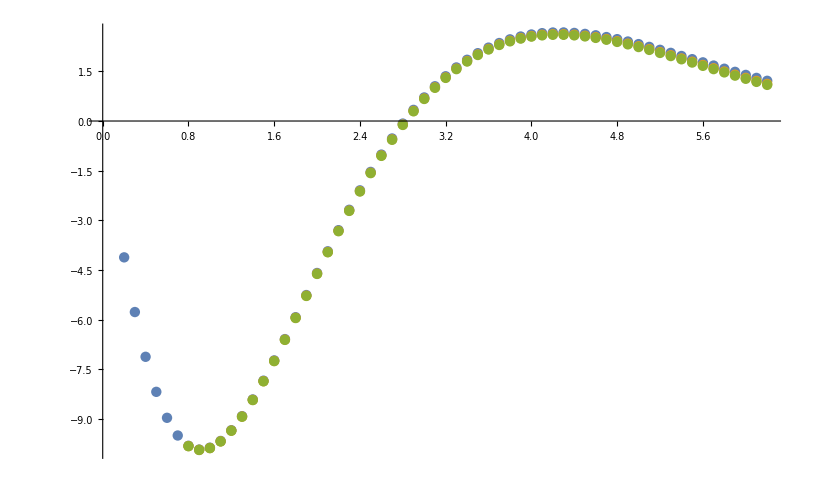

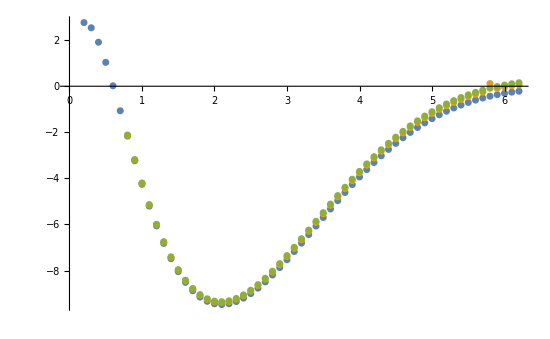

```mathematica
ListPlot[{wf10ImL,wf20ImL,wf30ImL}]
ListPlot[{wf10ReL,wf20ReL,wf30ReL}]
```

```mathematica
amp2w0reg
```

(9 ⅈ √3)/(2048 √(zb^2+zv^2+ω^2))+(171 (4+ⅈ √3) zb)/(4096 √2 ω √(zb^2+zv^2+ω^2))+(zb (36 ⅈ+369 √3+7 ⅈ ((-15-36 ⅈ)+(9+20 ⅈ) √3) π+7 (52 ⅈ+19 √3) Log[4]-504 Log[2+√3]-392 ⅈ √3 Log[2+√3]))/(1536 √2 π (zb^2+zv^2+ω^2))

```mathematica
FourierTransform[ta,zb,b]
```

(√(2/π) √(1/(zv^2+ω^2)) √(zv^2+ω^2) BesselK[0,b √(zv^2+ω^2) Sign[b]] (c[1]+ω c[2]))/ω+(ⅈ b ⅇ^(-Abs[b]/(√(1/(zv^2+ω^2)))) √(π/2) c[3])/Abs[b]

```mathematica
ta=c[2]/(√(zb^2+zv^2+ω^2))+(c[1]zb)/(ω √(zb^2+zv^2+ω^2))+c[3]/(zb^2+zv^2+ω^2)zb ;
tb=Assuming[b>0,FourierTransform[ta,zb,b]];
tb=Assuming[zv>0&&ω>0,tb/.b->1//Simplify]
```

((2 ⅈ √(zv^2+ω^2) BesselK[1,√(zv^2+ω^2)] c[1])/ω+2 BesselK[0,√(zv^2+ω^2)] c[2]+ⅈ ⅇ^(-√(zv^2+ω^2)) π c[3])/(√(2 π))

```mathematica
tb//Expand
```

(ⅈ √(2/π) √(zv^2+ω^2) BesselK[1,√(zv^2+ω^2)] c[1])/ω+√(2/π) BesselK[0,√(zv^2+ω^2)] c[2]+ⅈ ⅇ^(-√(zv^2+ω^2)) √(π/2) c[3]

```mathematica
amp2w0regIntzb=Assuming[b>0,FourierTransform[amp2w0reg,zb,b]];
```

```mathematica
amp2w0regIntzb=Assuming[zv>0&&ω>0,amp2w0regIntzb/.b->1//Simplify]
```

1/(12288 √π ω)ⅈ (54 √6 ω BesselK[0,√(zv^2+ω^2)]+513 (4+ⅈ √3) √(zv^2+ω^2) BesselK[1,√(zv^2+ω^2)]+4 ⅇ^(-√(zv^2+ω^2)) ω (36 ⅈ+369 √3+7 ⅈ ((-15-36 ⅈ)+(9+20 ⅈ) √3) π+7 (52 ⅈ+19 √3) Log[4]-504 Log[2+√3]-392 ⅈ √3 Log[2+√3]))

```mathematica
amp2w0regIntzb//Simplify
```

1/(12288 √π ω)ⅈ (54 √6 ω BesselK[0,√(zv^2+ω^2)]+513 (4+ⅈ √3) √(zv^2+ω^2) BesselK[1,√(zv^2+ω^2)]+4 ⅇ^(-√(zv^2+ω^2)) ω (36 ⅈ+369 √3+7 ⅈ ((-15-36 ⅈ)+(9+20 ⅈ) √3) π+7 (52 ⅈ+19 √3) Log[4]-504 Log[2+√3]-392 ⅈ √3 Log[2+√3]))

```mathematica
Monitor[wflistReg=Table[amp2w0regIntzbNum=amp2w0regIntzb/.ω->ii;NIntegrate[amp2w0regIntzbNum,{zv,0,∞},Method->"LocalAdaptive"],{ii,0.2,6.2,0.1}];,ii]
```

```mathematica
wfRegIm=Table[{0.2+0.1*ii,Im[wflistReg[[ii]]]},{ii,Length@wflistReg}];
wfRegRe=Table[{0.2+0.1*ii,Re[wflistReg[[ii]]]},{ii,Length@wflistReg}];
```

```mathematica
wfRegRe=Re/@wflistReg
```

{-0.255047+0.791755 ⅈ,-0.148369+0.536813 ⅈ,-0.0956884+0.405694 ⅈ,-0.0647946+0.324449 ⅈ,-0.0448852+0.268426 ⅈ,-0.0312925+0.227046 ⅈ,-0.0216596+0.195008 ⅈ,-0.0146622+0.169349 ⅈ,-0.00949674+0.148281 ⅈ,-0.00564615+0.130652 ⅈ,-0.00276234+0.115685 ⅈ,-0.000602424+0.102831 ⅈ,0.00100797+0.0916931 ⅈ,0.00219696+0.0819705 ⅈ,0.00306045+0.0734334 ⅈ,0.00367134+0.0659009 ⅈ,0.00408571+0.0592281 ⅈ,0.00434716+0.0532972 ⅈ,0.00448984+0.048011 ⅈ,0.00454066+0.0432882 ⅈ,0.00452094+0.0390604 ⅈ,0.00444762+0.0352692 ⅈ,0.0043342+0.0318646 ⅈ,0.00419141+0.0288032 ⅈ,0.00402783+0.0260476 ⅈ,0.00385025+0.0235647 ⅈ,0.00366408+0.0213259 ⅈ,0.00347357+0.0193055 ⅈ,0.00328206+0.0174812 ⅈ,0.00309213+0.015833 ⅈ,0.00290577+0.0143432 ⅈ,0.00272448+0.012996 ⅈ,0.00254936+0.0117773 ⅈ,0.00238118+0.0106744 ⅈ,0.00222048+0.00967609 ⅈ,0.00206756+0.00877213 ⅈ,0.0019226+0.00795345 ⅈ,0.00178561+0.00721183 ⅈ,0.00165651+0.0065399 ⅈ,0.00153516+0.005931 ⅈ,0.00142135+0.00537915 ⅈ,0.00131481+0.00487892 ⅈ,0.00121526+0.00442543 ⅈ,0.0011224+0.00401428 ⅈ,0.00103589+0.00364147 ⅈ,0.000955418+0.0033034 ⅈ,0.000880649+0.0029968 ⅈ,0.000811258+0.00271874 ⅈ,0.000746926+0.00246653 ⅈ,0.00068734+0.00223776 ⅈ,0.000632199+0.00203025 ⅈ,0.000581215+0.00184201 ⅈ,0.000534109+0.00167124 ⅈ,0.000490619+0.00151631 ⅈ,0.000450494+0.00137576 ⅈ,0.000413496+0.00124824 ⅈ,0.000379403+0.00113255 ⅈ,0.000348004+0.00102759 ⅈ,0.0003191+0.000932351 ⅈ,0.000292507+0.000845941 ⅈ,0.000268052+0.00076754 ⅈ}

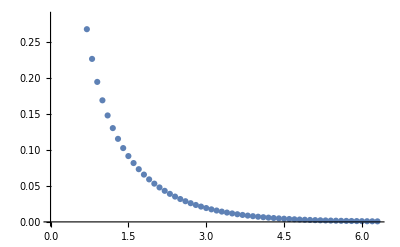

```mathematica
ListPlot[wfRegIm]
```

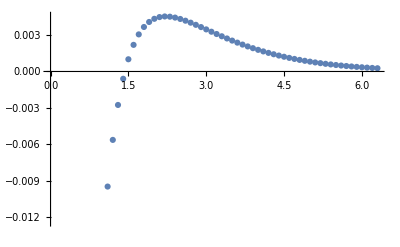

```mathematica
ListPlot[wfRegRe]
```

```mathematica
wfImFull=Table[{wfIm101[[ii,1]],wfIm101[[ii,2]]+wfRegIm[[ii,2]]},{ii,Length@wfIm101}]
```

{{0.2,0.750576},{0.3,0.479119},{0.4,0.334481},{0.5,0.242653},{0.6,0.178787},{0.7,0.132063},{0.8,0.0969164},{0.9,0.0701191},{1.,0.04962},{1.1,0.0340174},{1.2,0.0222971},{1.3,0.0136926},{1.4,0.00760373},{1.5,0.00354913},{1.6,0.0011351},{1.7,0.0000355169},{1.8,-0.0000222006},{1.9,0.000732937},{2.,0.00210804},{2.1,0.00394063},{2.2,0.00609411},{2.3,0.00845409},{2.4,0.0109254},{2.5,0.0134293},{2.6,0.0159017},{2.7,0.0182908},{2.8,0.0205557},{2.9,0.0226648},{3.,0.0245945},{3.1,0.0263283},{3.2,0.0278555},{3.3,0.0291704},{3.4,0.0302715},{3.5,0.0311609},{3.6,0.0318434},{3.7,0.0323264},{3.8,0.032619},{3.9,0.0327318},{4.,0.0326765},{4.1,0.0324654},{4.2,0.0321115},{4.3,0.031628},{4.4,0.0310281},{4.5,0.0303249},{4.6,0.0295313},{4.7,0.0286597},{4.8,0.0277221},{4.9,0.0267301},{5.,0.0256945},{5.1,0.0246256},{5.2,0.0235329},{5.3,0.0224253},{5.4,0.021311},{5.5,0.0201974},{5.6,0.0190915},{5.7,0.0179992},{5.8,0.0169262},{5.9,0.0158771},{6.,0.0148563},{6.1,0.0138674},{6.2,0.0129135}}

```mathematica
wfReFull=Table[{wfRe101[[ii,1]],wfRe101[[ii,2]]+wfRegRe[[ii,2]]},{ii,Length@wfRe101}]
```

{{0.2,-0.227427},{0.3,-0.123007},{0.4,-0.0765846},{0.5,-0.0544313},{0.6,-0.0446893},{0.7,-0.0419434},{0.8,-0.0432959},{0.9,-0.0470292},{1.,-0.052056},{1.1,-0.0576599},{1.2,-0.0633589},{1.3,-0.0688271},{1.4,-0.0738473},{1.5,-0.0782798},{1.6,-0.082041},{1.7,-0.0850889},{1.8,-0.0874117},{1.9,-0.0890203},{2.,-0.0899418},{2.1,-0.0902147},{2.2,-0.0898855},{2.3,-0.089006},{2.4,-0.0876304},{2.5,-0.0858145},{2.6,-0.0836135},{2.7,-0.0810817},{2.8,-0.0782713},{2.9,-0.0752321},{3.,-0.0720108},{3.1,-0.068651},{3.2,-0.0651931},{3.3,-0.0616737},{3.4,-0.0581264},{3.5,-0.0545811},{3.6,-0.0510647},{3.7,-0.0476006},{3.8,-0.0442096},{3.9,-0.0409092},{4.,-0.0377146},{4.1,-0.0346381},{4.2,-0.03169},{4.3,-0.0288783},{4.4,-0.0262092},{4.5,-0.0236869},{4.6,-0.0213142},{4.7,-0.0190922},{4.8,-0.017021},{4.9,-0.0150994},{5.,-0.0133252},{5.1,-0.0116954},{5.2,-0.0102063},{5.3,-0.00885341},{5.4,-0.00763187},{5.5,-0.00653631},{5.6,-0.00556108},{5.7,-0.00470024},{5.8,-0.00394769},{5.9,-0.0032972},{6.,-0.00274249},{6.1,-0.00227727},{6.2,-0.00189531}}

```mathematica
wfImFull10=Table[{wfImFull[[ii,1]],wfImFull[[ii,2]]*100},{ii,Length@wfImFull}];
```

```mathematica
wfImFull10
```

{{0.2,75.0576},{0.3,47.9119},{0.4,33.4481},{0.5,24.2653},{0.6,17.8787},{0.7,13.2063},{0.8,9.69164},{0.9,7.01191},{1.,4.962},{1.1,3.40174},{1.2,2.22971},{1.3,1.36926},{1.4,0.760373},{1.5,0.354913},{1.6,0.11351},{1.7,0.00355169},{1.8,-0.00222006},{1.9,0.0732937},{2.,0.210804},{2.1,0.394063},{2.2,0.609411},{2.3,0.845409},{2.4,1.09254},{2.5,1.34293},{2.6,1.59017},{2.7,1.82908},{2.8,2.05557},{2.9,2.26648},{3.,2.45945},{3.1,2.63283},{3.2,2.78555},{3.3,2.91704},{3.4,3.02715},{3.5,3.11609},{3.6,3.18434},{3.7,3.23264},{3.8,3.2619},{3.9,3.27318},{4.,3.26765},{4.1,3.24654},{4.2,3.21115},{4.3,3.1628},{4.4,3.10281},{4.5,3.03249},{4.6,2.95313},{4.7,2.86597},{4.8,2.77221},{4.9,2.67301},{5.,2.56945},{5.1,2.46256},{5.2,2.35329},{5.3,2.24253},{5.4,2.1311},{5.5,2.01974},{5.6,1.90915},{5.7,1.79992},{5.8,1.69262},{5.9,1.58771},{6.,1.48563},{6.1,1.38674},{6.2,1.29135}}

```mathematica
wfReFull10=Table[{wfReFull[[ii,1]],wfReFull[[ii,2]]*100},{ii,Length@wfReFull}];
```

```mathematica
wfReFull10
```

{{0.2,-22.7427},{0.3,-12.3007},{0.4,-7.65846},{0.5,-5.44313},{0.6,-4.46893},{0.7,-4.19434},{0.8,-4.32959},{0.9,-4.70292},{1.,-5.2056},{1.1,-5.76599},{1.2,-6.33589},{1.3,-6.88271},{1.4,-7.38473},{1.5,-7.82798},{1.6,-8.2041},{1.7,-8.50889},{1.8,-8.74117},{1.9,-8.90203},{2.,-8.99418},{2.1,-9.02147},{2.2,-8.98855},{2.3,-8.9006},{2.4,-8.76304},{2.5,-8.58145},{2.6,-8.36135},{2.7,-8.10817},{2.8,-7.82713},{2.9,-7.52321},{3.,-7.20108},{3.1,-6.8651},{3.2,-6.51931},{3.3,-6.16737},{3.4,-5.81264},{3.5,-5.45811},{3.6,-5.10647},{3.7,-4.76006},{3.8,-4.42096},{3.9,-4.09092},{4.,-3.77146},{4.1,-3.46381},{4.2,-3.169},{4.3,-2.88783},{4.4,-2.62092},{4.5,-2.36869},{4.6,-2.13142},{4.7,-1.90922},{4.8,-1.7021},{4.9,-1.50994},{5.,-1.33252},{5.1,-1.16954},{5.2,-1.02063},{5.3,-0.885341},{5.4,-0.763187},{5.5,-0.653631},{5.6,-0.556108},{5.7,-0.470024},{5.8,-0.394769},{5.9,-0.32972},{6.,-0.274249},{6.1,-0.227727},{6.2,-0.189531}}

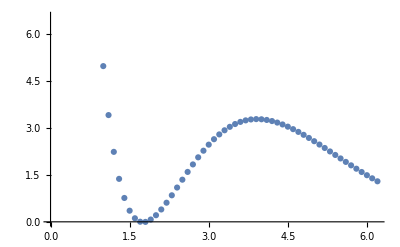

```mathematica
ListPlot[wfImFull10]
```

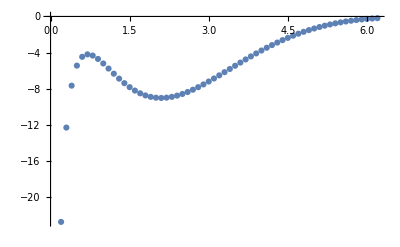

```mathematica
ListPlot[wfReFull10]
```

## TBD

### RegularizedTest2

```mathematica
ampReg3=((9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 ω (zv+ii)))* Exp[-I zb-0.001Abs[zb]];
```

```mathematica
NIntegrate[zb Exp[-I zb-0.001Abs[zb]],{zb,-200 π-π,200 π+π}]
```

-1.16707×10^-12-671.645 ⅈ

```mathematica
FourierTransform[zb Exp[-I zb-0.00000001Abs[zb]],zb,x]
```

(0.+1.59577×10^-8 ⅈ)/(-1.+1. x)^3

```mathematica
ampNumReg3=ampReg3/.ω->1;
```

```mathematica
Monitor[wf1listzvtest2=Table[NIntegrate[ampNumReg3,{zv,0,80},{zb,-20 π-π,20 π+π},Method->"LocalAdaptive"],{ii,20}];,ii]
```

```mathematica
wf1listzvtest2
```

{27.7562-64.1002 ⅈ,23.4557-54.1684 ⅈ,20.9712-48.4309 ⅈ,19.2298-44.4093 ⅈ,17.8951-41.327 ⅈ,16.8174-38.8381 ⅈ,15.9168-36.7582 ⅈ,15.1456-34.9772 ⅈ,14.473-33.4239 ⅈ,13.8781-32.0501 ⅈ,13.3459-30.821 ⅈ,12.8654-29.7112 ⅈ,12.4281-28.7013 ⅈ,12.0275-27.7764 ⅈ,11.6586-26.9244 ⅈ,11.3171-26.1357 ⅈ,10.9996-25.4025 ⅈ,10.7034-24.7184 ⅈ,10.426-24.0778 ⅈ,10.1655-23.4762 ⅈ}

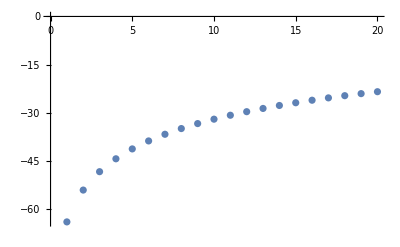

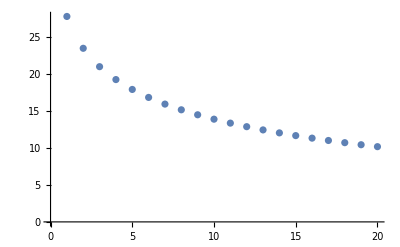

```mathematica
ListPlot[{Im/@wf1listzvtest2}]
ListPlot[{Re/@wf1listzvtest2}]
```

### RegularizedTest

```mathematica
ampReg2=(amp2-(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 ω (zv+ii)))* Exp[-I zb-0.001Abs[zb]];
```

```mathematica
ampNumReg2=ampReg2/.ω->1;
```

```mathematica
Monitor[wf1listzvtest1=Table[NIntegrate[ampNumReg2,{zv,0,80},{zb,-20 π-π,20 π+π},Method->"LocalAdaptive"],{ii,5}];,ii]
```

```mathematica
wf1listzvtest1
```

{-21.3933+48.6444 ⅈ,-17.0925+38.712 ⅈ,-14.608+32.9743 ⅈ,-12.8667+28.9532 ⅈ,-11.5326+25.8713 ⅈ}

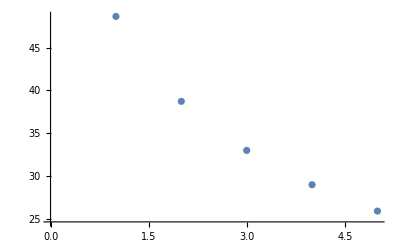

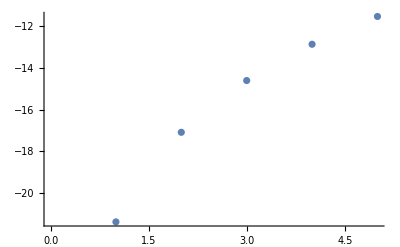

```mathematica
ListPlot[{Im/@wf1listzvtest1}]
ListPlot[{Re/@wf1listzvtest1}]
```

### Regularizedzvm2

```mathematica
reg1=Series[(amp2),{zv,∞,1}]//Normal;
```

```mathematica
reg2=Series[(amp2-reg1),{zv,∞,2}]//Normal;
```

```mathematica
reg1=reg1/.zv->zv+1;
```

```mathematica
reg2=reg2/.zv->zv+1;
```

```mathematica
ampReg=(amp2-reg1-reg2)* Exp[-I zb-0.001Abs[zb]];
```

```mathematica
ampNumReg=ampReg/.ω->1//Expand;
```

```mathematica
Monitor[wf1listzv1=Table[NIntegrate[ampNumReg,{zv,0,ii*10},{zb,-20 π-π,20 π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

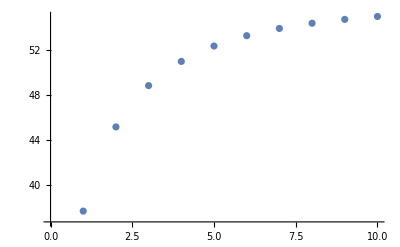

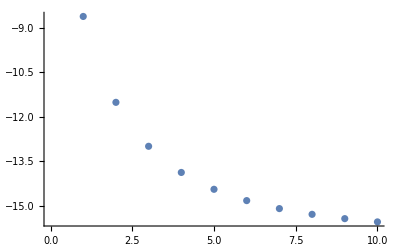

```mathematica
ListPlot[{Im/@wf1listzv1}]
ListPlot[{Re/@wf1listzv1}]
```

### UnRegularized

```mathematica
ampUnReg=(amp2)* Exp[-I zb-0.001Abs[zb]];
```

```mathematica
ampNumUnReg=ampUnReg/.ω->1;
```

```mathematica
NIntegrate[ampNumReg,{zv,0,1000},{zb,-2*0 π-π,2*0 π+π},Method->"LocalAdaptive"]
```

-0.285564-0.301724 ⅈ

```mathematica
NIntegrate[ampNumReg,{zv,0,1000},{zb,-100* π-π,100* π+π},Method->"LocalAdaptive"]
```

$Aborted

```mathematica
Monitor[wf1list5=Table[NIntegrate[ampNumUnReg,{zv,0,1000},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

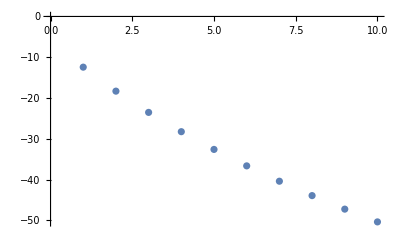

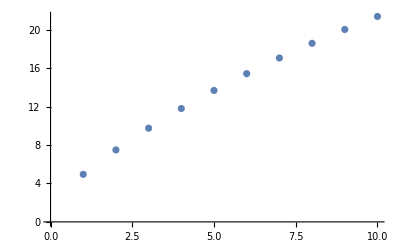

```mathematica
ListPlot[{Im/@wf1list5}]
ListPlot[{Re/@wf1list5}]
```

```mathematica
Monitor[wf1list6=Table[NIntegrate[ampNumUnReg,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

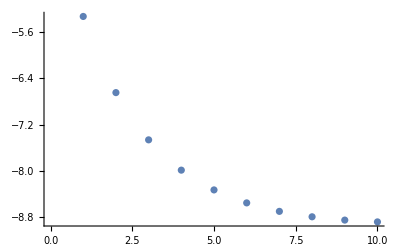

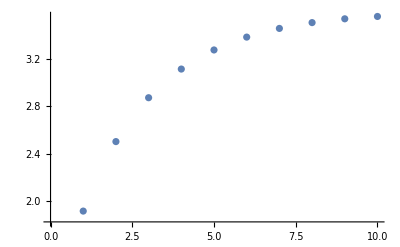

```mathematica
ListPlot[{Im/@wf1list6}]
ListPlot[{Re/@wf1list6}]
```

### UnRegularized

```mathematica
NIntegrate[(amp2)* Exp[-I zb-0.001Abs[zb]]/.ω->1,{zv,0,1},{zb,-∞,∞},Method->"GlobalAdaptive"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zb near {zv,zb} = {1.,-2360.66}. NIntegrate obtained -0.0108448-0.217904 ⅈ and 3.41511×10^-7 for the integral and error estimates.

-0.0108448-0.217904 ⅈ

```mathematica
Integrate[(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 ω (zv+10)),zv]
```

(9 (19 √2 (4+ⅈ √3) zb+4 ⅈ √3 ω) Log[10+zv])/(8192 ω)

```mathematica
Log[10]//N
```

2.30259

```mathematica
Monitor[wf1list6=Table[ampNum=(amp2) Exp[-I zb-0.001Abs[zb]]/.ω->1+0.1ii//Expand;NIntegrate[ampNum,{zv,0,100},{zb,-20 π-π,20 π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

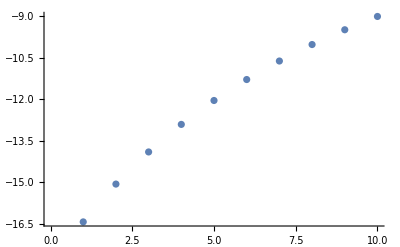

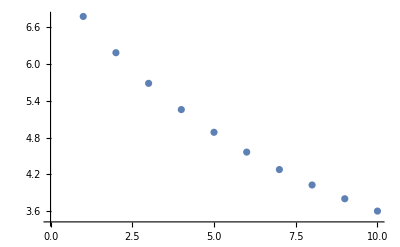

```mathematica
ListPlot[{Im/@wf1list6}]
ListPlot[{Re/@wf1list6}]
```

```mathematica
Monitor[wf1list7=Table[ampNum=(amp2) Exp[-I zb-0.001Abs[zb]]/.ω->1+0.1ii//Expand;NIntegrate[ampNum,{zv,0,100},{zb,-20 π-π,20 π+π},Method->"LocalAdaptive"],{ii,30}];,ii]
```

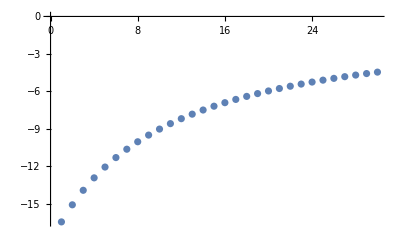

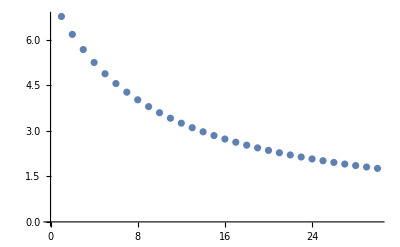

```mathematica
ListPlot[{Im/@wf1list7}]
ListPlot[{Re/@wf1list7}]
```

```mathematica
Monitor[wf1list8=Table[ampNum=(amp2) Exp[-I zb-0.001Abs[zb]]/.ω->1+0.5ii//Expand;NIntegrate[ampNum,{zv,0,100},{zb,-20 π-π,20 π+π},Method->"LocalAdaptive"],{ii,30}];,ii]
```

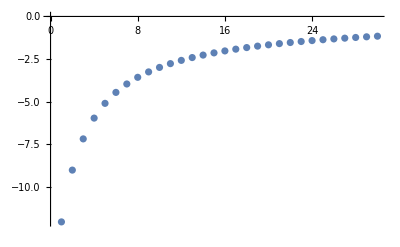

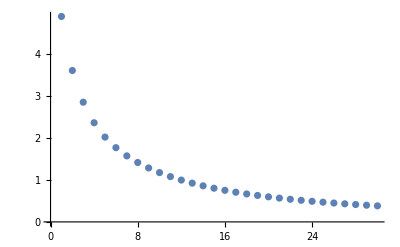

```mathematica
ListPlot[{Im/@wf1list8}]
ListPlot[{Re/@wf1list8}]
```

```mathematica
wf1list6
```

{6.77489-16.4403 ⅈ,6.1837-15.0728 ⅈ,5.68403-13.9114 ⅈ,5.25612-12.9153 ⅈ,4.88568-12.0506 ⅈ,4.56237-11.2928 ⅈ,4.27792-10.6234 ⅈ,4.02616-10.0273 ⅈ,3.80164-9.49332 ⅈ,3.60046-9.01232 ⅈ}

```mathematica
ListPlot[{Im/@wf1list6}]
ListPlot[{Re/@wf1list6}]
```

-Graphics-

-Graphics-

```mathematica
Monitor[wf1list5p=Table[NIntegrate[ampNum,{zv,0,ii*10},{zb,-20 π-π,20 π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

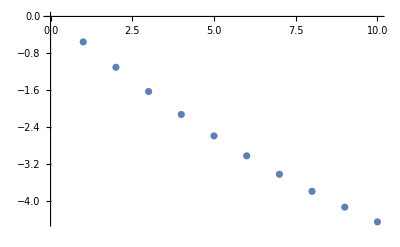

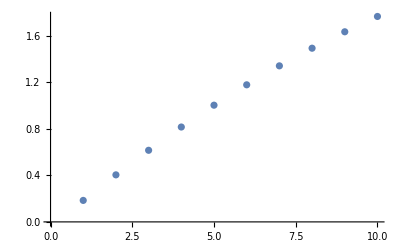

```mathematica
ListPlot[{Im/@wf1list5p}]
ListPlot[{Re/@wf1list5p}]
```

```mathematica
Monitor[wf1list5=Table[NIntegrate[ampNum,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

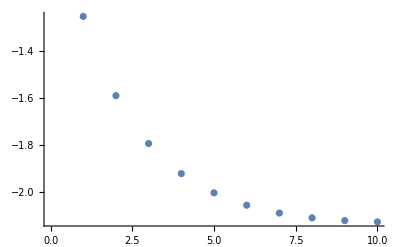

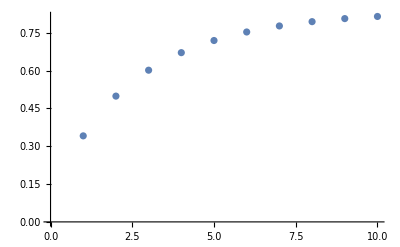

```mathematica
ListPlot[{Im/@wf1list5}]
ListPlot[{Re/@wf1list5}]
```

```mathematica
Monitor[wf1list4=Table[NIntegrate[ampNum,{zv,0,30},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
Monitor[wf1list3=Table[NIntegrate[ampNum,{zv,0,20},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
Monitor[wf1list2=Table[NIntegrate[ampNum,{zv,0,10},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
Monitor[wf1list=Table[NIntegrate[ampNum,{zv,0,1},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
wf1list
```

{0.0803557-0.458896 ⅈ,0.0835374-0.455111 ⅈ,0.0846697-0.452435 ⅈ,0.0850486-0.450255 ⅈ,0.0850732-0.44833 ⅈ,0.0849065-0.446556 ⅈ,0.0846244-0.444877 ⅈ,0.0842684-0.443266 ⅈ,0.0838628-0.441704 ⅈ,0.0834226-0.440181 ⅈ}

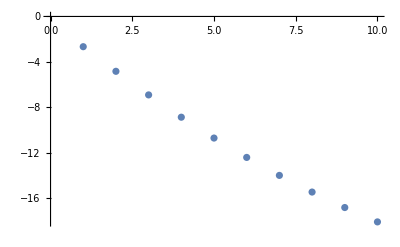

```mathematica
ListPlot[{Im/@wf1list6}]
```

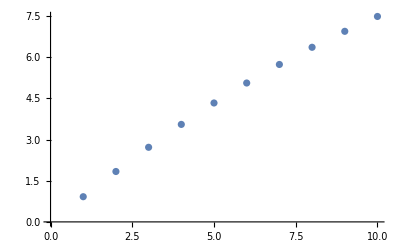

```mathematica
ListPlot[{Re/@wf1list6}]
```

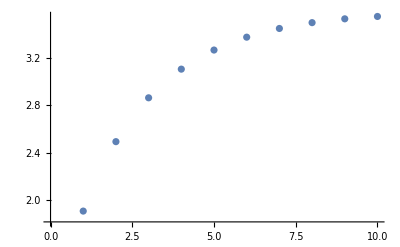

```mathematica
ListPlot[{Re/@wf1list5}]
```

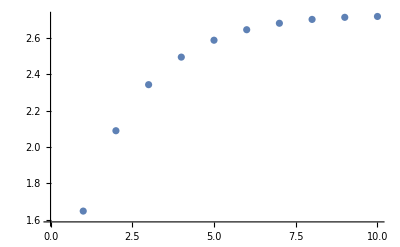

```mathematica
ListPlot[{Re/@wf1list4}]
```

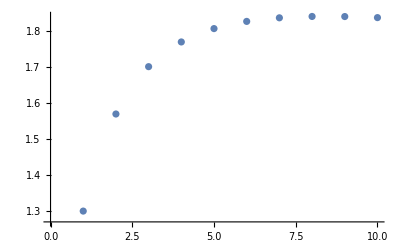

```mathematica
ListPlot[{Re/@wf1list2}]
```

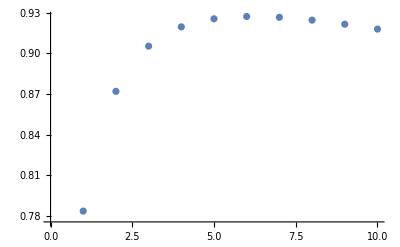

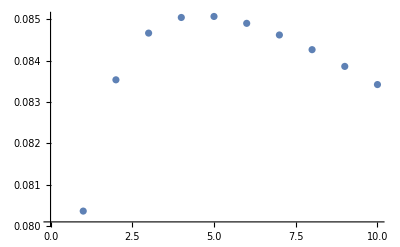

```mathematica
ListPlot[{Re/@wf1list2}]
ListPlot[{Re/@wf1list}]
```

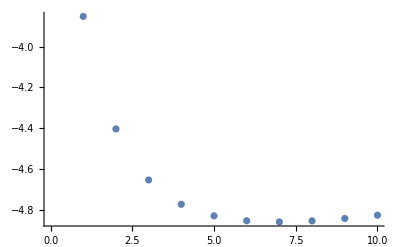

```mathematica
ListPlot[{Im/@wf1list2}]
```

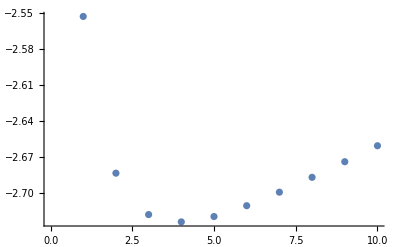

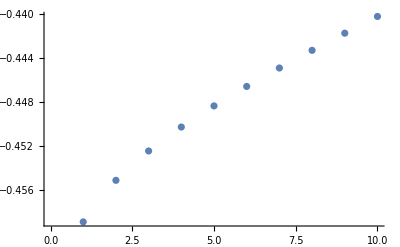

```mathematica
ListPlot[{Im/@wf1list2}]
ListPlot[{Im/@wf1list}]
```

```mathematica
amp2Inv=amp2/.zv->1/zv;
```

```mathematica
Series[amp2Inv,{zv,0,1}]
```

(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω) zv)/(8192 √(1/zv^2) zv ω)+O[zv]^2

```mathematica
ampInvNum=(1/zv^2 amp2Inv-(9  (19 √2 (4+ⅈ √3) zb+4 ⅈ √3 ω))/(zv 8192 ω))* Exp[-I zb-0.001Abs[zb]]/.ω->1//Expand;
```

```mathematica
ampInvNum/.zv->1/.zb->0.5
```

-0.0296485-0.0414069 ⅈ

```mathematica
Monitor[wf2list=Table[NIntegrate[ampInvNum,{zv,0,10},{zb,-ii π,ii π},Method->"LocalAdaptive"],{ii,20}];,ii]
```

```mathematica
Monitor[wf2list=Table[NIntegrate[ampInvNum,{zv,0,10},{zb,-ii π,ii π},Method->"LocalAdaptive"],{ii,20}];,ii]
```

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

```mathematica
wf1list
```

{0.0688142-0.463277 ⅈ,-0.0982787+0.0257256 ⅈ,0.0803557-0.458896 ⅈ,-0.10406+0.020991 ⅈ,0.0835374-0.455111 ⅈ,-0.105932+0.0178785 ⅈ,0.0846697-0.452435 ⅈ,-0.106609+0.0154949 ⅈ,0.0850486-0.450255 ⅈ,-0.106782+0.0134608 ⅈ,0.0850732-0.44833 ⅈ,-0.106699+0.0116194 ⅈ,0.0849065-0.446556 ⅈ,-0.106466+0.00989731 ⅈ,0.0846244-0.444877 ⅈ,-0.106144+0.0082564 ⅈ,0.0842684-0.443266 ⅈ,-0.105758+0.00667081 ⅈ,0.0838628-0.441704 ⅈ,-0.105336+0.00513084 ⅈ}

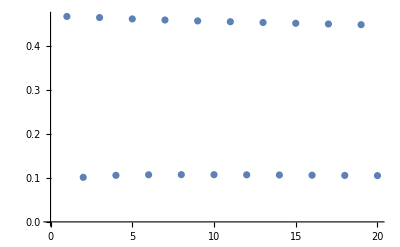

```mathematica
ListPlot[{Norm/@wf1list}]
```

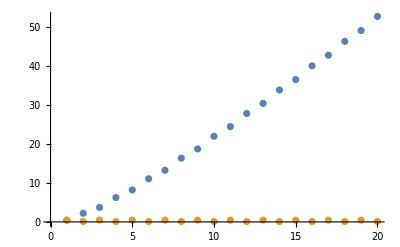

```mathematica
ListPlot[{Norm/@wf2list,Norm/@wf1list}]
```

```mathematica
Assuming[zv>0,amp2Inv[[1]]//PowerExpand]
```

(89667 zb^10)/(2048 √(zb^2+1/zv^2+(4 ω^2)/3) (3 zb^2+3/zv^2-3 √2 zb ω-(3 √2 ω)/zv+4 ω^2) (3 zb^2+3/zv^2-(6 zb)/zv+8 ω^2)^4)

```mathematica
NIntegrate[(1/zv^2 amp2Inv-(9  (19 √2 (4+ⅈ √3) zb+4 ⅈ √3 ω))/(zv 8192 ω))* Exp[-I zb-0.001Abs[zb]]/.ω->1,{zv,0.01,1},{zb,-∞,∞},Method->"GlobalAdaptive",WorkingPrecision->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
NIntegrate[(amp2-(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 ω (zv+100000000)))* Exp[-I zb-0.001Abs[zb]]/.ω->1,{zv,0,1},{zb,-∞,∞},Method->"GlobalAdaptive"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zb near {zv,zb} = {1.,-2360.66}. NIntegrate obtained -0.0108448-0.217904 ⅈ and 3.41484×10^-7 for the integral and error estimates.

-0.0108448-0.217904 ⅈ

```mathematica
NIntegrate[(amp2)* Exp[-I zb-0.001Abs[zb]]/.ω->1,{zv,0,10},{zb,-∞,∞},Method->"GlobalAdaptive"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zb near {zv,zb} = {10.,-2360.66}. NIntegrate obtained -0.0213348-0.446433 ⅈ and 3.93602×10^-6 for the integral and error estimates.

-0.0213348-0.446433 ⅈ

```mathematica
NIntegrate[(amp2)* Exp[-I zb]/.ω->1,{zv,0,50},{zb,-1000,1000},Method->"GlobalAdaptive"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.89332+6.19533 ⅈ and 0.00982855 for the integral and error estimates.

-2.89332+6.19533 ⅈ

```mathematica
0.6555741183155361-2.2392561436860032 ⅈ
```

```mathematica
NIntegrate[(amp2RegPole1)* Exp[-I zb],{zv,2.4,2.41},{zb,-10,10},Method->"GlobalAdaptive"]
```

59851.3-2.18279×10^-11 ⅈ

```mathematica
Monitor[amp2RegPole1V=Table[NIntegrate[(amp2list[[pole1[[ii]]]]-ampPole[[pole1[[ii]]]])* Exp[-I zb],{zv,0,2.4},{zb,-10,10},Method->"GlobalAdaptive"],{ii,Length@pole1}];,ii]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
Monitor[amp2RegPole2V=Table[NIntegrate[(amp2list[[pole2[[ii]]]]-ampPole2[[pole2[[ii]]]])* Exp[-I zb],{zv,0,2.4},{zb,-10,10},Method->"GlobalAdaptive"],{ii,Length@pole2}];,ii]
```

```mathematica
amp2RegPole2V//Total
```

{-3481.04-2940.46 ⅈ}

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.497232-0.40591 ⅈ and 0.0220157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.178689-0.147495 ⅈ and 0.024005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.250318-0.297798 ⅈ and 0.0339308 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
amp2RegPole1V//Total
```

{-16773.6+13949.9 ⅈ}

```mathematica
(Norm/@amp2RegPole1V)
```

41000.8

```mathematica
Monitor[amp2RegPole1V2=Table[NIntegrate[(amp2list[[pole1[[ii]]]]-ampPole[[pole1[[ii]]]])* Exp[-I zb],{zv,2.5,10},{zb,-10,10},Method->"GlobalAdaptive"],{ii,Length@pole1}];,ii]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
amp2RegPole1V//Total
```

{-20240.2+16735.6 ⅈ}

```mathematica
amp2RegPole1V2//Total
```

{-21009.2+17122.5 ⅈ}

```mathematica
pole1
```

{{1525},{1526},{1527},{1528},{1529},{1530},{1531},{1532},{1533},{1534},{1535},{1536},{1537},{1538},{1539},{1540},{1541},{1542},{1543},{1544},{1545},{1546},{1547},{1548},{1549},{1550},{1551},{1552},{1553},{1554},{1555},{1556},{1557},{1558},{1559},{1560},{1561},{1562},{1563},{1564},{1565},{1566},{1567},{1568},{1569},{1570},{1571},{1572},{1573},{1574},{1575},{1576},{1577},{1578},{1579},{1580},{1581},{1582},{1583},{1584},{1585},{1586},{1587},{1588},{1589},{1590},{1867},{1868},{1869},{1870},{1871},{1872},{1873},{1874},{1875},{1876},{1877},{1878},{1879},{1880},{1881},{1882},{1883},{1884},{1885},{1886},{1887},{1888},{1889},{1890},{1891},{1892},{1893},{1894},{1895},{1896},{1897},{1898},{1899},{1900},{1901},{1902},{1903},{1904},{1905},{1906},{1907},{1908},{1909},{1910},{1911},{1912},{1913},{1914},{1915},{1916},{1917},{1918},{1919},{1920},{1921},{1922},{1923},{1924},{1925},{1926},{1927},{1928},{1929},{1930},{1931},{1932},{1933},{1934},{1935},{1936},{1937},{1938},{1939},{1940},{1941},{1942},{1943},{1944},{1945},{1946},{1947},{1948},{1949},{1950},{1951},{1952},{1953},{1954},{1955},{1956},{1957},{1958},{1959},{1960},{1961},{1962},{1963},{1964},{1965},{1966},{1967},{1968},{1969},{1970},{1971},{1972},{1973},{1974},{1975},{1976},{1977},{1978},{1979},{1980},{1981},{1982},{1983},{1984},{1985},{1986},{1987},{1988},{1989},{1990},{1991},{1992},{1993},{1994},{1995},{1996},{1997},{1998},{1999},{2000},{2001},{2002},{2003},{2004},{2005},{2006},{2007},{2008},{2009},{2010},{2011},{2012},{2013},{2160},{2161},{2162},{2163},{2164},{2165},{2166},{2167},{2168},{2169},{2170},{2171},{2172},{2173},{2174},{2175},{2176},{2177},{2178},{2179},{2180},{2181},{2182},{2183},{2184},{2185},{2186},{2187},{2188},{2189},{2190},{2191},{2192},{2193},{2194},{2195},{2196},{2197},{2198},{2199},{2200},{2201},{2202},{2203},{2204},{2205},{2206},{2207},{2208},{2209},{2210},{2211},{2212},{2213},{2214},{2215},{2216},{2217},{2218},{2219},{2220},{2221},{2222},{2223},{2224},{2225},{2226},{2227},{2228},{2229},{2230},{2231},{2232},{2233},{2234},{2235},{2236},{2237},{2238},{2239},{2240},{2241},{2242},{2243},{2244},{2245},{2246},{2247},{2248},{2249},{2250},{2251},{2252},{2253},{2254},{2255},{2256},{2257},{2258},{2259},{2260},{2261},{2262},{2263},{2264},{2265},{2266},{2267},{2268},{2269},{2270},{2271},{2272},{2273},{2274},{2275},{2276},{2277},{2278},{2279},{2280},{2281},{2282},{2283},{2284},{2285},{2286},{2287},{2288},{2289},{2290},{2291},{2292},{2293},{2294},{2295},{2296},{2297},{2298},{2299},{2300},{2301},{2302},{2303},{2304},{2305},{2803},{2804},{2805},{2806},{2807},{2808},{2809},{2810},{2811},{2812},{2813},{2814},{2815},{2816},{2817},{2818},{2819},{2820},{2821},{2822},{2823},{2824},{2825},{2826},{2827},{2828},{2829},{2830},{2831},{2832},{2833},{2834},{2835},{2836},{2837},{2838},{2839},{2840},{2841},{2842},{2843},{2844},{2845},{2846},{2847},{2848},{2849},{2850},{2851},{2852},{2853},{2854},{2855},{2856},{2857},{2858},{2859},{2860},{2861},{2862},{2863},{2864},{2865},{2866},{2867},{2868},{2869},{2870},{2871},{2872},{2873},{2874},{2875},{2876},{2877},{2878},{2879},{2880},{2881},{2882},{2883},{2884},{2885},{2886},{2887},{2888},{2889},{2890},{2891},{2892},{2893},{2894},{2895},{2896},{2897},{2898},{2899},{2900},{2901},{2902},{2903},{2904},{2905},{2906},{2907},{2908},{2909},{2910},{2911},{2912},{2913},{2914},{2915},{2916},{2917},{2918},{2919},{2920},{2921},{2922},{2923},{2924},{2925},{2926},{2927},{2928},{2929},{2930},{2931},{2932},{2933},{2934},{2935},{2936},{2937},{2938},{2939},{2940},{2941},{2942},{2943},{2944},{2945},{2946},{2947},{2948},{2949}}

```mathematica
Monitor[int1=Table[NIntegrate[(amp2RegPole1[[ii]])* Exp[-I zb],{zv,0,10},{zb,-10,10},Method->"GlobalAdaptive"],{ii,Length@amp2RegPole1}];,ii]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zv near {zv,zb} = {2.44949,-2.44939}. NIntegrate obtained -1.38049×10^14+1.14425×10^14 ⅈ and 1.89642×10^13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zv near {zv,zb} = {2.44949,-2.44939}. NIntegrate obtained -1.38049×10^14+1.14425×10^14 ⅈ and 1.89642×10^13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zv near {zv,zb} = {2.44949,-2.44939}. NIntegrate obtained -1.38049×10^14+1.14425×10^14 ⅈ and 1.89642×10^13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

```mathematica
amp3=amp2-ampPole-ampPole2;
```

```mathematica
Monitor[ampinfzv=Sum[Series[amp3[[ii]],{zv,∞,1}]//Normal,{ii,Length@amp3}];,ii]
```

```mathematica
ampinfzv
```

-14265/(512 zv)+(41959 ⅈ √3)/(4096 zv)+(351 ⅈ √(3/2) (-3 √2-8 zb))/(8192 zv)-(3335 (-3 √2-8 zb))/(2048 √2 zv)-(5539 ⅈ √(3/2) zb)/(4096 zv)+(2713 zb)/(1024 √2 zv)-(351 ⅈ √(3/2) (3 √2+8 zb))/(8192 zv)+(3335 (3 √2+8 zb))/(2048 √2 zv)-(39 ⅈ √(3/2) (27 √2+16 zb))/(2048 zv)-(-8521563 √2+4920931 √6-13664347 √2 Log[4]+7889885 √6 Log[4]-30115880 √2 Log[2+√3]+17387539 √6 Log[2+√3]-14977651 √2 Log[4+2 √3]+8647501 √6 Log[4+2 √3])/(393216 (-2+√3)^5 (2+√3) π zv)

```mathematica
amp4=amp3-ampinfzv;
```

```mathematica
Monitor[ampinf=Sum[Series[amp4[[ii]],{zb,∞,1}]//Normal,{ii,Length@amp4}];,ii]
```

```mathematica
amp5=amp4-ampinf;
```

```mathematica
int1=NIntegrate[(amp5)* Exp[-I zb],{zv,0,10},{zb,-10,10},Method->"GlobalAdaptive"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zv near {zv,zb} = {2.44949,-2.44939}. NIntegrate obtained -1.38049×10^14+1.14425×10^14 ⅈ and 1.89642×10^13 for the integral and error estimates.

-1.38049×10^14+1.14425×10^14 ⅈ

```mathematica
amp2[[2123]]//Apart[#,zv]&//Apart[#,zb]&//Expand
```

$Aborted

This is the contribution to the waveform coming from c2 * I2:

```mathematica
amp5m13m22/.{i1->0,i2->0,R->0,dIR->0,lq->0,ly->0,lw1->0,lw2->0}/.c1->0/.replaceTriangleIntegrals/.replacec2(*/.replacec1*);
%//.{F1->FTrace[Momentum[v1],{FieldStr[k]},Momentum[q1]],F2->FTrace[Momentum[v2],{FieldStr[k]},Momentum[q2]],F3->FTrace[Momentum[v1],{FieldStr[k]},Momentum[v2]]};
%//.FTrace[a_,{FieldStr[k_]},b_]:>DotProduct[a,Momentum[k]]DotProduct[b,EpsilonPol[k]]-DotProduct[b,Momentum[k]]DotProduct[a,EpsilonPol[k]];
%//.{qq1->-DotProduct[Momentum[q1],Momentum[q1]],qq2->-DotProduct[Momentum[q2],Momentum[q2]],w1->DotProduct[Momentum[v1],Momentum[k]],w2->DotProduct[Momentum[v2],Momentum[k]],y->DotProduct[Momentum[v1],Momentum[v2]]};
%//.{v2->u2,v1->u1,y->γ};
%/.{Momentum[q2]->Momentum[k]-Momentum[q1]};
Sqrt[(γ^2-1)]%//.{Momentum[q1]->z1 Momentum[u1]+z2 Momentum[u2]+zb Momentum[bt]+zv Momentum[vt]};
%//.{DotProduct[Momentum[u1],Momentum[u2]]->γ,DotProduct[Momentum[bt],Momentum[bt]]->-1,DotProduct[Momentum[vt],Momentum[vt]]->-1,DotProduct[Momentum[u1],Momentum[u1]]->1,DotProduct[Momentum[u2],Momentum[u2]]->1};
%//.{DotProduct[Momentum[u1],Momentum[bt]]->0,DotProduct[Momentum[u2],Momentum[bt]]->0,DotProduct[Momentum[u1],Momentum[vt]]->0,DotProduct[Momentum[u2],Momentum[vt]]->0,DotProduct[Momentum[vt],Momentum[bt]]->0};
%/.{z1->(DotProduct[Momentum[u2],Momentum[k]] γ)/(-1+γ^2),z2->-DotProduct[Momentum[u2],Momentum[k]]/(-1+γ^2)};
%/.{Momentum[bt]->Momentum[b]/Sqrt[-DotProduct[Momentum[b],Momentum[b]]],Momentum[vt]->Momentum[v]/(4Sqrt[-DotProduct[Momentum[b],Momentum[b]](γ^2-1)])}/.γ->DotProduct[Momentum[u1],Momentum[u2]]//parametrise;
%/.{V->(√(-1+γ^2))/γ,B->b};
(*%//Reduce`FreeVariables*)
%/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->2,ω->3}//Simplify;
amp1=%+ReplaceAll[%,zv->-zv]//Simplify
%//Series[#,zv->Infinity]&
%%//Series[#,{zb,Infinity,0}]&
```

(24 (9922 ⅈ+13025 √3) zb^20-√2 (1053 ⅈ+13340 √3) zb^21-2 √2 zb^19 (3 (451767 ⅈ+549344 √3)+(104961 ⅈ+260284 √3) zv^2)+12 zb^18 (6 (789611 ⅈ+674428 √3)+(1243767 ⅈ+1010468 √3) zv^2)-√2 zb^17 (417553002 ⅈ+314643672 √3+6 (27942789 ⅈ+18681664 √3) zv^2+97 (24825 ⅈ+36364 √3) zv^4)+12 zb^16 (451356066 ⅈ+281625606 √3+6 (40645703 ⅈ+20487396 √3) zv^2+(12112639 ⅈ+6352482 √3) zv^4)-12 √2 zb^15 (9 (271929819 ⅈ+154276490 √3)+9 (179896339 ⅈ+77299132 √3) zv^2+6 (20989683 ⅈ+8796572 √3) zv^4+26 (33557 ⅈ+30492 √3) zv^6)+24 zb^14 (108 (110958679 ⅈ+54403094 √3)+9 (1006889239 ⅈ+358904506 √3) zv^2+12 (82904599 ⅈ+25603520 √3) zv^4+(23814574 ⅈ+7490736 √3) zv^6)-2 √2 zb^13 (3888 (158158657 ⅈ+73131462 √3)+54 (9573518859 ⅈ+3010685914 √3) zv^2+18 (3956432571 ⅈ+1008673756 √3) zv^4+12 (224626755 ⅈ+53775508 √3) zv^6+7 (1727907 ⅈ+831460 √3) zv^8)+72 zb^12 (864 (156505959 ⅈ+63702952 √3)+1008 (119188339 ⅈ+31908188 √3) zv^2+15 (1313126201 ⅈ+266053414 √3) zv^4+4 (267519603 ⅈ+43449656 √3) zv^6+2 (8346919 ⅈ+1172943 √3) zv^8)-12 √2 zb^11 (31104 (91147941 ⅈ+36013870 √3)+1296 (2037306799 ⅈ+491551762 √3) zv^2+9 (54933911799 ⅈ+9336667346 √3) zv^4+(33962284719 ⅈ+4154410572 √3) zv^6+(837566637 ⅈ+73479336 √3) zv^8+(2831297 ⅈ+268060 √3) zv^10)-24 zb^10 (-124416 (74888211 ⅈ+26255534 √3)-5184 (1679914563 ⅈ+344006476 √3) zv^2-108 (16644299705 ⅈ+2227591754 √3) zv^4-9 (16556979927 ⅈ+1372821170 √3) zv^6-18 (294980799 ⅈ+11111620 √3) zv^8+(-62809561 ⅈ+965148 √3) zv^10)-12 (24+zv^2)^4 (-252685910016 ⅈ+22892544 (-2813 ⅈ+236 √3) zv^2+5184 (-1468959 ⅈ+147964 √3) zv^4+432 (-1445573 ⅈ+225606 √3) zv^6+18 (-1647908 ⅈ+470703 √3) zv^8+6 (-155199 ⅈ+64684 √3) zv^10+(-18791 ⅈ+12710 √3) zv^12)+2 √2 zb^9 (-1492992 (216687357 ⅈ+74925802 √3)-186624 (1624344211 ⅈ+300955762 √3) zv^2-1296 (52226585361 ⅈ+5732584054 √3) zv^4-54 (119680860951 ⅈ+6616601794 √3) zv^6-144 (2019803832 ⅈ+12834257 √3) zv^8+6 (-901675575 ⅈ+48007288 √3) zv^10+(-15193365 ⅈ+4335652 √3) zv^12)-24 zb^8 (-2985984 (49420412 ⅈ+15054315 √3)-497664 (268259103 ⅈ+40706864 √3) zv^2-2592 (12105970393 ⅈ+959330352 √3) zv^4-216 (15469993577 ⅈ+392956926 √3) zv^6+9 (-20274621503 ⅈ+462531788 √3) zv^8+6 (-816604737 ⅈ+63130684 √3) zv^10+(-48287097 ⅈ+7834654 √3) zv^12)+√2 zb (24+zv^2)^3 (-3439853568 (14347 ⅈ+1756 √3)+23887872 (-832707 ⅈ+64879 √3) zv^2+62208 (-46500507 ⅈ+9258094 √3) zv^4+20736 (-12578325 ⅈ+3440809 √3) zv^6+108 (-153838041 ⅈ+53221978 √3) zv^8+18 (-37157883 ⅈ+14701916 √3) zv^10+6 (-2551161 ⅈ+1191008 √3) zv^12+(-29565 ⅈ+117572 √3) zv^14)-12 zb^2 (24+zv^2)^2 (-573308928 (215707 ⅈ+26500 √3)+5971968 (-10121397 ⅈ+263608 √3) zv^2+124416 (-91719911 ⅈ+11148578 √3) zv^4+10368 (-114794587 ⅈ+20546824 √3) zv^6+216 (-367141251 ⅈ+80381026 √3) zv^8+18 (-189062981 ⅈ+51765818 √3) zv^10+6 (-14478395 ⅈ+5288084 √3) zv^12+(-1064463 ⅈ+620812 √3) zv^14)+4 √2 zb^7 (-8957952 (234637671 ⅈ+70616210 √3)-5971968 (307766262 ⅈ+41154563 √3) zv^2-1928448 (233823429 ⅈ+13294382 √3) zv^4-18144 (2887461801 ⅈ+2613134 √3) zv^6+27 (-122071575345 ⅈ+6014764834 √3) zv^8+27 (-4126749033 ⅈ+433390796 √3) zv^10+18 (-94521259 ⅈ+18300908 √3) zv^12+(-4256838 ⅈ+2923448 √3) zv^14)-24 zb^6 (-35831808 (43766971 ⅈ+11244462 √3)-2985984 (429810825 ⅈ+43013474 √3) zv^2-6220800 (51594965 ⅈ+1349146 √3) zv^4+93312 (-425124013 ⅈ+11328340 √3) zv^6+108 (-25835143177 ⅈ+1910989590 √3) zv^8+27 (-4231268287 ⅈ+525683494 √3) zv^10+12 (-209139075 ⅈ+39890504 √3) zv^12+(-22027318 ⅈ+6720416 √3) zv^14)+6 √2 zb^3 (24+zv^2) (-2293235712 (1026951 ⅈ+198295 √3)-11943936 (119345595 ⅈ+1699906 √3) zv^2+746496 (-421113621 ⅈ+32889626 √3) zv^4+10368 (-3643624305 ⅈ+511498498 √3) zv^6+432 (-6538751589 ⅈ+1240135834 √3) zv^8+54 (-2521592951 ⅈ+603546206 √3) zv^10+18 (-223494713 ⅈ+69529116 √3) zv^12+(-59706495 ⅈ+27403088 √3) zv^14+(-139787 ⅈ+259500 √3) zv^16)-24 zb^4 (-859963392 (12009407 ⅈ+2390956 √3)-1003290624 (7213957 ⅈ+342020 √3) zv^2+8957952 (-202893149 ⅈ+6491344 √3) zv^4+2488320 (-97585979 ⅈ+8231362 √3) zv^6+2592 (-7667386153 ⅈ+977813112 √3) zv^8+864 (-1206616798 ⅈ+208076809 √3) zv^10+9 (-3833948887 ⅈ+876834286 √3) zv^12+12 (-54530863 ⅈ+16924560 √3) zv^14+5 (-1072264 ⅈ+477183 √3) zv^16)+√2 zb^5 (-859963392 (82190559 ⅈ+20684746 √3)-35831808 (1516396923 ⅈ+122466586 √3) zv^2-5971968 (2305628553 ⅈ+1567406 √3) zv^4+746496 (-2400012915 ⅈ+132753358 √3) zv^6+2592 (-53170128309 ⅈ+5492070242 √3) zv^8+324 (-20053233035 ⅈ+3088366118 √3) zv^10+1764 (-101370645 ⅈ+22267964 √3) zv^12+24 (-98170923 ⅈ+33748036 √3) zv^14+(-5505273 ⅈ+6392212 √3) zv^16))/(8192 √3 √(12+zb^2+zv^2) (12-3 √2 zb+zb^2-3 √2 zv+zv^2) (12-3 √2 zb+zb^2+3 √2 zv+zv^2) (24+zb^2-2 zb zv+zv^2)^4 (24+zb^2+2 zb zv+zv^2)^4)

(225492 ⅈ-152520 √3-29565 ⅈ √2 zb+117572 √6 zb)/(8192 √3 zv)+O[1/zv]^3

-(1053 ⅈ+13340 √3)/(4096 √6)+O[1/zb]^1

```mathematica
solmin=Solve[{D[(12-3 √2 zb+zb^2+3 √2 zv+zv^2) ,zb]==0,D[(12-3 √2 zb+zb^2+3 √2 zv+zv^2) ,zv]==0}]
```

{{zb→3/(√2),zv→-3/(√2)}}

```mathematica
(12-3 √2 zb+zb^2+3 √2 zv+zv^2) /.solmin
```

{3}

```mathematica
Plot3D[{(12-3 √2 zb+zb^2-3 √2 zv+zv^2)},{zb,-1,1},{zv,-1,1}]
```

-Graphics3D-

```mathematica
NIntegrate[amp1//Expand//N,{zb,-1000,1000},{zv,-10000,10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-1.68055×10^18+2.84708×10^22 ⅈ

The contribution to the waveform from the log contributions:

```mathematica
amp5m13m22/.{i1->0,i2->0,dIR->0,c1->0,c2->0}/.replaceDivergences/.amp5TreeLevel->0/.replacer[]/.replacelq[]/.replacely[]/.replacelw2[]
%//.{F1->FTrace[Momentum[v1],{FieldStr[k]},Momentum[q1]],F2->FTrace[Momentum[v2],{FieldStr[k]},Momentum[q2]],F3->FTrace[Momentum[v1],{FieldStr[k]},Momentum[v2]]};
%//.FTrace[a_,{FieldStr[k_]},b_]:>DotProduct[a,Momentum[k]]DotProduct[b,EpsilonPol[k]]-DotProduct[b,Momentum[k]]DotProduct[a,EpsilonPol[k]];
%//.{qq1->-DotProduct[Momentum[q1],Momentum[q1]],qq2->-DotProduct[Momentum[q2],Momentum[q2]],w1->DotProduct[Momentum[v1],Momentum[k]],w2->DotProduct[Momentum[v2],Momentum[k]],y->DotProduct[Momentum[v1],Momentum[v2]]};
%//.{v2->u2,v1->u1,y->γ};
%/.{Momentum[q2]->Momentum[k]-Momentum[q1]};
Sqrt[(γ^2-1)]%//.{Momentum[q1]->z1 Momentum[u1]+z2 Momentum[u2]+zb Momentum[bt]+zv Momentum[vt]}
%//.{DotProduct[Momentum[u1],Momentum[u2]]->γ,DotProduct[Momentum[bt],Momentum[bt]]->-1,DotProduct[Momentum[vt],Momentum[vt]]->-1,DotProduct[Momentum[u1],Momentum[u1]]->1,DotProduct[Momentum[u2],Momentum[u2]]->1};
%//.{DotProduct[Momentum[u1],Momentum[bt]]->0,DotProduct[Momentum[u2],Momentum[bt]]->0,DotProduct[Momentum[u1],Momentum[vt]]->0,DotProduct[Momentum[u2],Momentum[vt]]->0,DotProduct[Momentum[vt],Momentum[bt]]->0};
%/.{z1->(DotProduct[Momentum[u2],Momentum[k]] γ)/(-1+γ^2),z2->-DotProduct[Momentum[u2],Momentum[k]]/(-1+γ^2)};
%/.{Momentum[bt]->Momentum[b]/Sqrt[-DotProduct[Momentum[b],Momentum[b]]],Momentum[vt]->Momentum[v]/(4Sqrt[-DotProduct[Momentum[b],Momentum[b]](γ^2-1)])}/.γ->DotProduct[Momentum[u1],Momentum[u2]]//parametrise;
%/.{V->(√(-1+γ^2))/γ,B->b};
%/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->2,ω->3};
amp2=%+ReplaceAll[%,zv->-zv];
%//Series[#,zv->Infinity]&;
%//Simplify
```

(-(-F3^2 w2+F3^2 w1 y+4 F3^2 w2 y^2-4 F3^2 w1 y^3-4 F3^2 w2 y^4+4 F3^2 w1 y^5)/(256 w1 w2 (-1+y) (1+y) (w1^2+w2^2-2 w1 w2 y))-1/(49152 7 (1+y))-(-5 F3^2 qq1^4 w1^2+679)/1)/π+(((F1 1)/1-1) Log[qq1/qq2])/π+((1) Log[1])/π+((-(F3^2 (3 w1^2 w2+17+1))/(256 w1^2 (1) (1+y) (1)^2)-1/1) Log[y+1])/(π √(-1+y^2))
 |  |  |  |

√(-1+γ^2) ((-(-ku2 (ku2 ku1-ku1 ku2)^2+6+4 ku1 (1)^2 u1u2^5)/(256 ku1 ku2 (-1+u1u2) (1+u1u2) (ku1^2+ku2^2-2 ku1 ku2 u1u2))-1/1-1/(49152 7 1^3))/π+((1) Log[ku2^2/ku1^2])/π+((1) Log[u1u2+1])/(π √(-1+u1u2^2))+((-1/(24576 2 ((11)^2)-1/1) Log[1/1])/π)
 |  |  |  |

1/(6144 √3 π zv^2)(3 (132199-33687 ⅈ √3+4 ⅈ (5559 ⅈ+364 √3) Log[4]+32 (225 ⅈ+1108 √3) Log[2+√3])+2 √2 zb (7 (495-52 ⅈ √3) Log[4]-6 (-9919+6250 ⅈ √3+4 (-49 ⅈ+195 √3) Log[2+√3])))+O[1/zv]^3

The integration is zv is convergent after symmetrisation. (we may still want to remove the local terms in zb).

```mathematica
amp2=amp2//Expand;
```

```mathematica
NIntegrate[amp2 Exp[-I 0.0001 zb],{zb,-∞,∞},{zv,0,∞},Method->"GlobalAdaptive"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in zb near {zb,zv} = {9.35671×10^10,1.16959×10^10}. NIntegrate obtained 4.90905×10^22+2.43547×10^22 ⅈ and 5.47888×10^22 for the integral and error estimates.

4.90905×10^22+2.43547×10^22 ⅈ

```mathematica
Denominator[amp//2]
```

1

#### Tree-level (convergent in zv after symmetrisation)

```mathematica
amp5TreeLevel/.replaceTree
%//.{F1->FTrace[Momentum[v1],{FieldStr[k]},Momentum[q1]],F2->FTrace[Momentum[v2],{FieldStr[k]},Momentum[q2]],F3->FTrace[Momentum[v1],{FieldStr[k]},Momentum[v2]]};
%//.FTrace[a_,{FieldStr[k_]},b_]:>DotProduct[a,Momentum[k]]DotProduct[b,EpsilonPol[k]]-DotProduct[b,Momentum[k]]DotProduct[a,EpsilonPol[k]];
%//.{qq1->-DotProduct[Momentum[q1],Momentum[q1]],qq2->-DotProduct[Momentum[q2],Momentum[q2]],w1->DotProduct[Momentum[v1],Momentum[k]],w2->DotProduct[Momentum[v2],Momentum[k]],y->DotProduct[Momentum[v1],Momentum[v2]]};
%//.{v2->u2,v1->u1,y->γ};
%/.{Momentum[q2]->Momentum[k]-Momentum[q1]};
Sqrt[(γ^2-1)]%//.{Momentum[q1]->z1 Momentum[u1]+z2 Momentum[u2]+zb Momentum[bt]+zv Momentum[vt]};
%//.{DotProduct[Momentum[u1],Momentum[u2]]->γ,DotProduct[Momentum[bt],Momentum[bt]]->-1,DotProduct[Momentum[vt],Momentum[vt]]->-1,DotProduct[Momentum[u1],Momentum[u1]]->1,DotProduct[Momentum[u2],Momentum[u2]]->1};
%//.{DotProduct[Momentum[u1],Momentum[bt]]->0,DotProduct[Momentum[u2],Momentum[bt]]->0,DotProduct[Momentum[u1],Momentum[vt]]->0,DotProduct[Momentum[u2],Momentum[vt]]->0,DotProduct[Momentum[vt],Momentum[bt]]->0}//Together
%/.{z1->(DotProduct[Momentum[u2],Momentum[k]] γ)/(-1+γ^2),z2->-DotProduct[Momentum[u2],Momentum[k]]/(-1+γ^2)};
%/.{Momentum[bt]->Momentum[b]/Sqrt[-DotProduct[Momentum[b],Momentum[b]]],Momentum[vt]->Momentum[v]/(4Sqrt[-DotProduct[Momentum[b],Momentum[b]](γ^2-1)])}/.γ->DotProduct[Momentum[u1],Momentum[u2]]//Together
%//parametrise;
Exp[-I zb b]%/.{V->(√(-1+γ^2))/γ,B->b};
%/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->2,ω->3}//Simplify
%+ReplaceAll[%,zv->-zv]//Series[#,zv->Infinity]&
```

(ⅈ F3 (-4 F3 w1 w2+2 F3 (qq1+qq2) y-4 F2 w1 y+4 F1 w2 y))/(4 qq1 qq2 w1 w2)+(ⅈ (-1/2 F2 F3 (qq1+qq2) w1+F2^2 w1^2+1/2 F1 F3 (qq1+qq2) w2+F1^2 w2^2) (1-2 y^2))/(4 qq1 qq2 w1^2 w2^2)

-((ⅈ √(-1+γ^2) (-2 z1^2 zb ku2^2 btk ku1^2-2 z2^2 zb ku2^2 btk ku1^2+2 zb^3 ku2^2 btk ku1^2+2 zb zv^2 ku2^2 btk ku1^2-4 z1 z2 zb γ ku2^2 btk ku1^2+4 z1^2 zb γ^2 ku2^2 btk ku1^2+4 z2^2 zb γ^2 ku2^2 btk ku1^2-4 zb^3 γ^2 ku2^2 btk ku1^2-4 zb zv^2 γ^2 ku2^2 btk ku1^2+8 z1 z2 zb γ^3 ku2^2 btk ku1^2+2 z1^2 ku2^2 k ku1^2+2 z2^2 ku2^2 k ku1^2-2 zb^2 ku2^2 k ku1^2-2 zv^2 ku2^2 k ku1^2+4 z1 z2 γ ku2^2 k ku1^2-4 z1^2 γ^2 ku2^2 k ku1^2-4 z2^2 γ^2 ku2^2 k ku1^2+4 zb^2 γ^2 ku2^2 k ku1^2+4 zv^2 γ^2 ku2^2 k ku1^2-8 z1 z2 γ^3 ku2^2 k ku1^2+zb ku2^2 btk k ku1^2-2 zb γ^2 ku2^2 btk k ku1^2-ku2^2 k^2 ku1^2+2 γ^2 ku2^2 k^2 ku1^2-2 z1^3 ku2^2 ku1^3-2 z1 z2^2 ku2^2 ku1^3+2 z1 zb^2 ku2^2 ku1^3+2 z1 zv^2 ku2^2 ku1^3-4 z1^2 z2 γ ku2^2 ku1^3+4 z1^3 γ^2 ku2^2 ku1^3+4 z1 z2^2 γ^2 ku2^2 ku1^3-4 z1 zb^2 γ^2 ku2^2 ku1^3-4 z1 zv^2 γ^2 ku2^2 ku1^3+8 z1^2 z2 γ^3 ku2^2 ku1^3+z1 ku2^2 k ku1^3-2 z1 γ^2 ku2^2 k ku1^3-2 z1^2 ku1 ku2 k ku1 ku2-2 z2^2 ku1 ku2 k ku1 ku2+2 zb^2 ku1 ku2 k ku1 ku2+2 zv^2 ku1 ku2 k ku1 ku2-4 z1 z2 γ ku1 ku2 k ku1 ku2+4 z1^2 γ^2 ku1 ku2 k ku1 ku2+4 z2^2 γ^2 ku1 ku2 k ku1 ku2-4 zb^2 γ^2 ku1 ku2 k ku1 ku2-4 zv^2 γ^2 ku1 ku2 k ku1 ku2+8 z1 z2 γ^3 ku1 ku2 k ku1 ku2+2 zb ku1 ku2 btk k ku1 ku2-4 zb γ^2 ku1 ku2 btk k ku1 ku2-ku1 ku2 k^2 ku1 ku2+2 γ^2 ku1 ku2 k^2 ku1 ku2+4 z1^2 zb kbt ku2 ku1^2 ku2+4 z2^2 zb kbt ku2 ku1^2 ku2-4 zb^3 kbt ku2 ku1^2 ku2-4 zb zv^2 kbt ku2 ku1^2 ku2+8 z1 z2 zb γ kbt ku2 ku1^2 ku2-8 z1^2 zb γ^2 kbt ku2 ku1^2 ku2-8 z2^2 zb γ^2 kbt ku2 ku1^2 ku2+8 zb^3 γ^2 kbt ku2 ku1^2 ku2+8 zb zv^2 γ^2 kbt ku2 ku1^2 ku2-16 z1 z2 zb γ^3 kbt ku2 ku1^2 ku2-2 z1^2 kk ku2 ku1^2 ku2-2 z2^2 kk ku2 ku1^2 ku2+2 zb^2 kk ku2 ku1^2 ku2+2 zv^2 kk ku2 ku1^2 ku2-4 z1 z2 γ kk ku2 ku1^2 ku2+4 z1^2 γ^2 kk ku2 ku1^2 ku2+4 z2^2 γ^2 kk ku2 ku1^2 ku2-4 zb^2 γ^2 kk ku2 ku1^2 ku2-4 zv^2 γ^2 kk ku2 ku1^2 ku2+8 z1 z2 γ^3 kk ku2 ku1^2 ku2+4 z1^3 ku1 ku2 ku1^2 ku2+4 z1 z2^2 ku1 ku2 ku1^2 ku2-4 z1 zb^2 ku1 ku2 ku1^2 ku2-4 z1 zv^2 ku1 ku2 ku1^2 ku2+8 z1^2 z2 γ ku1 ku2 ku1^2 ku2-8 z1^3 γ^2 ku1 ku2 ku1^2 ku2-8 z1 z2^2 γ^2 ku1 ku2 ku1^2 ku2+8 z1 zb^2 γ^2 ku1 ku2 ku1^2 ku2+8 z1 zv^2 γ^2 ku1 ku2 ku1^2 ku2-16 z1^2 z2 γ^3 ku1 ku2 ku1^2 ku2+2 z1^2 z2 ku2^2 ku1^2 ku2+2 z2^3 ku2^2 ku1^2 ku2-2 z2 zb^2 ku2^2 ku1^2 ku2-2 z2 zv^2 ku2^2 ku1^2 ku2+4 z1 z2^2 γ ku2^2 ku1^2 ku2-4 z1^2 z2 γ^2 ku2^2 ku1^2 ku2-4 z2^3 γ^2 ku2^2 ku1^2 ku2+4 z2 zb^2 γ^2 ku2^2 ku1^2 ku2+4 z2 zv^2 γ^2 ku2^2 ku1^2 ku2-8 z1 z2^2 γ^3 ku2^2 ku1^2 ku2+4 z1^2 zv ku2 kvt ku1^2 ku2+4 z2^2 zv ku2 kvt ku1^2 ku2-4 zb^2 zv ku2 kvt ku1^2 ku2-4 zv^3 ku2 kvt ku1^2 ku2+8 z1 z2 zv γ ku2 kvt ku1^2 ku2-8 z1^2 zv γ^2 ku2 kvt ku1^2 ku2-8 z2^2 zv γ^2 ku2 kvt ku1^2 ku2+8 zb^2 zv γ^2 ku2 kvt ku1^2 ku2+8 zv^3 γ^2 ku2 kvt ku1^2 ku2-16 z1 z2 zv γ^3 ku2 kvt ku1^2 ku2-2 zb kk ku2 btk ku1^2 ku2+4 zb γ^2 kk ku2 btk ku1^2 ku2-2 zb kbt ku2 k ku1^2 ku2+4 zb γ^2 kbt ku2 k ku1^2 ku2+3 kk ku2 k ku1^2 ku2-6 γ^2 kk ku2 k ku1^2 ku2-z2 ku2^2 k ku1^2 ku2+2 z2 γ^2 ku2^2 k ku1^2 ku2-2 zv ku2 kvt k ku1^2 ku2+4 zv γ^2 ku2 kvt k ku1^2 ku2-2 z1 kk ku2 ku1^3 ku2+4 z1 γ^2 kk ku2 ku1^3 ku2+8 z1^2 γ ku2^2 ku1^3 ku2+8 z2^2 γ ku2^2 ku1^3 ku2-8 zb^2 γ ku2^2 ku1^3 ku2-8 zv^2 γ ku2^2 ku1^3 ku2+16 z1 z2 γ^2 ku2^2 ku1^3 ku2-4 γ ku2^2 k ku1^3 ku2+2 z1^2 zb ku1^2 btk ku2^2+2 z2^2 zb ku1^2 btk ku2^2-2 zb^3 ku1^2 btk ku2^2-2 zb zv^2 ku1^2 btk ku2^2+4 z1 z2 zb γ ku1^2 btk ku2^2-4 z1^2 zb γ^2 ku1^2 btk ku2^2-4 z2^2 zb γ^2 ku1^2 btk ku2^2+4 zb^3 γ^2 ku1^2 btk ku2^2+4 zb zv^2 γ^2 ku1^2 btk ku2^2-8 z1 z2 zb γ^3 ku1^2 btk ku2^2-4 zb^2 ku1^2 btk^2 ku2^2+8 zb^2 γ^2 ku1^2 btk^2 ku2^2+zb ku1^2 btk k ku2^2-2 zb γ^2 ku1^2 btk k ku2^2-4 z1^2 zb kbt ku1 ku1 ku2^2-4 z2^2 zb kbt ku1 ku1 ku2^2+4 zb^3 kbt ku1 ku1 ku2^2+4 zb zv^2 kbt ku1 ku1 ku2^2-8 z1 z2 zb γ kbt ku1 ku1 ku2^2+8 z1^2 zb γ^2 kbt ku1 ku1 ku2^2+8 z2^2 zb γ^2 kbt ku1 ku1 ku2^2-8 zb^3 γ^2 kbt ku1 ku1 ku2^2-8 zb zv^2 γ^2 kbt ku1 ku1 ku2^2+16 z1 z2 zb γ^3 kbt ku1 ku1 ku2^2+2 z1^2 kk ku1 ku1 ku2^2+2 z2^2 kk ku1 ku1 ku2^2-2 zb^2 kk ku1 ku1 ku2^2-2 zv^2 kk ku1 ku1 ku2^2+4 z1 z2 γ kk ku1 ku1 ku2^2-4 z1^2 γ^2 kk ku1 ku1 ku2^2-4 z2^2 γ^2 kk ku1 ku1 ku2^2+4 zb^2 γ^2 kk ku1 ku1 ku2^2+4 zv^2 γ^2 kk ku1 ku1 ku2^2-8 z1 z2 γ^3 kk ku1 ku1 ku2^2-2 z1^3 ku1^2 ku1 ku2^2-2 z1 z2^2 ku1^2 ku1 ku2^2+2 z1 zb^2 ku1^2 ku1 ku2^2+2 z1 zv^2 ku1^2 ku1 ku2^2-4 z1^2 z2 γ ku1^2 ku1 ku2^2+4 z1^3 γ^2 ku1^2 ku1 ku2^2+4 z1 z2^2 γ^2 ku1^2 ku1 ku2^2-4 z1 zb^2 γ^2 ku1^2 ku1 ku2^2-4 z1 zv^2 γ^2 ku1^2 ku1 ku2^2+8 z1^2 z2 γ^3 ku1^2 ku1 ku2^2-4 z1^2 z2 ku1 ku2 ku1 ku2^2-4 z2^3 ku1 ku2 ku1 ku2^2+4 z2 zb^2 ku1 ku2 ku1 ku2^2+4 z2 zv^2 ku1 ku2 ku1 ku2^2-8 z1 z2^2 γ ku1 ku2 ku1 ku2^2+8 z1^2 z2 γ^2 ku1 ku2 ku1 ku2^2+8 z2^3 γ^2 ku1 ku2 ku1 ku2^2-8 z2 zb^2 γ^2 ku1 ku2 ku1 ku2^2-8 z2 zv^2 γ^2 ku1 ku2 ku1 ku2^2+16 z1 z2^2 γ^3 ku1 ku2 ku1 ku2^2-4 z1^2 zv ku1 kvt ku1 ku2^2-4 z2^2 zv ku1 kvt ku1 ku2^2+4 zb^2 zv ku1 kvt ku1 ku2^2+4 zv^3 ku1 kvt ku1 ku2^2-8 z1 z2 zv γ ku1 kvt ku1 ku2^2+8 z1^2 zv γ^2 ku1 kvt ku1 ku2^2+8 z2^2 zv γ^2 ku1 kvt ku1 ku2^2-8 zb^2 zv γ^2 ku1 kvt ku1 ku2^2-8 zv^3 γ^2 ku1 kvt ku1 ku2^2+16 z1 z2 zv γ^3 ku1 kvt ku1 ku2^2+8 zb^2 kbt ku1 btk ku1 ku2^2-16 zb^2 γ^2 kbt ku1 btk ku1 ku2^2-2 zb kk ku1 btk ku1 ku2^2+4 zb γ^2 kk ku1 btk ku1 ku2^2+8 z2 zb ku1 ku2 btk ku1 ku2^2-16 z2 zb γ^2 ku1 ku2 btk ku1 ku2^2+8 zb zv ku1 kvt btk ku1 ku2^2-16 zb zv γ^2 ku1 kvt btk ku1 ku2^2-2 zb kbt ku1 k ku1 ku2^2+4 zb γ^2 kbt ku1 k ku1 ku2^2+kk ku1 k ku1 ku2^2-2 γ^2 kk ku1 k ku1 ku2^2-z1 ku1^2 k ku1 ku2^2+2 z1 γ^2 ku1^2 k ku1 ku2^2-2 zv ku1 kvt k ku1 ku2^2+4 zv γ^2 ku1 kvt k ku1 ku2^2-4 zb^2 kbt^2 ku1^2 ku2^2+8 zb^2 γ^2 kbt^2 ku1^2 ku2^2+4 zb kbt kk ku1^2 ku2^2-8 zb γ^2 kbt kk ku1^2 ku2^2-2 kk^2 ku1^2 ku2^2+4 γ^2 kk^2 ku1^2 ku2^2+2 z1 kk ku1 ku1^2 ku2^2-4 z1 γ^2 kk ku1 ku1^2 ku2^2-8 z2 zb kbt ku2 ku1^2 ku2^2+16 z2 zb γ^2 kbt ku2 ku1^2 ku2^2+2 z2 kk ku2 ku1^2 ku2^2-4 z2 γ^2 kk ku2 ku1^2 ku2^2-16 z1^2 γ ku1 ku2 ku1^2 ku2^2-16 z2^2 γ ku1 ku2 ku1^2 ku2^2+16 zb^2 γ ku1 ku2 ku1^2 ku2^2+16 zv^2 γ ku1 ku2 ku1^2 ku2^2-32 z1 z2 γ^2 ku1 ku2 ku1^2 ku2^2-4 z2^2 ku2^2 ku1^2 ku2^2+8 z2^2 γ^2 ku2^2 ku1^2 ku2^2-8 zb zv kbt kvt ku1^2 ku2^2+16 zb zv γ^2 kbt kvt ku1^2 ku2^2+4 zv kk kvt ku1^2 ku2^2-8 zv γ^2 kk kvt ku1^2 ku2^2-8 z2 zv ku2 kvt ku1^2 ku2^2+16 z2 zv γ^2 ku2 kvt ku1^2 ku2^2-4 zv^2 kvt^2 ku1^2 ku2^2+8 zv^2 γ^2 kvt^2 ku1^2 ku2^2+16 zb γ ku1 ku2 btk ku1^2 ku2^2-16 zb γ kbt ku2 ku1^3 ku2^2+8 γ kk ku2 ku1^3 ku2^2-16 z2 γ ku2^2 ku1^3 ku2^2-16 zv γ ku2 kvt ku1^3 ku2^2+8 ku2^2 ku1^4 ku2^2+2 z1^2 z2 ku1^2 ku2^3+2 z2^3 ku1^2 ku2^3-2 z2 zb^2 ku1^2 ku2^3-2 z2 zv^2 ku1^2 ku2^3+4 z1 z2^2 γ ku1^2 ku2^3-4 z1^2 z2 γ^2 ku1^2 ku2^3-4 z2^3 γ^2 ku1^2 ku2^3+4 z2 zb^2 γ^2 ku1^2 ku2^3+4 z2 zv^2 γ^2 ku1^2 ku2^3-8 z1 z2^2 γ^3 ku1^2 ku2^3-8 z2 zb ku1^2 btk ku2^3+16 z2 zb γ^2 ku1^2 btk ku2^3+z2 ku1^2 k ku2^3-2 z2 γ^2 ku1^2 k ku2^3+8 z2 zb kbt ku1 ku1 ku2^3-16 z2 zb γ^2 kbt ku1 ku1 ku2^3-2 z2 kk ku1 ku1 ku2^3+4 z2 γ^2 kk ku1 ku1 ku2^3+8 z1^2 γ ku1^2 ku1 ku2^3+8 z2^2 γ ku1^2 ku1 ku2^3-8 zb^2 γ ku1^2 ku1 ku2^3-8 zv^2 γ ku1^2 ku1 ku2^3+16 z1 z2 γ^2 ku1^2 ku1 ku2^3+8 z2^2 ku1 ku2 ku1 ku2^3-16 z2^2 γ^2 ku1 ku2 ku1 ku2^3+8 z2 zv ku1 kvt ku1 ku2^3-16 z2 zv γ^2 ku1 kvt ku1 ku2^3-16 zb γ ku1^2 btk ku1 ku2^3+4 γ ku1^2 k ku1 ku2^3+16 zb γ kbt ku1 ku1^2 ku2^3-8 γ kk ku1 ku1^2 ku2^3+32 z2 γ ku1 ku2 ku1^2 ku2^3+16 zv γ ku1 kvt ku1^2 ku2^3-16 ku1 ku2 ku1^3 ku2^3-4 z2^2 ku1^2 ku2^4+8 z2^2 γ^2 ku1^2 ku2^4-16 z2 γ ku1^2 ku1 ku2^4+8 ku1^2 ku1^2 ku2^4-2 z1^2 zv ku2^2 ku1^2 kvt-2 z2^2 zv ku2^2 ku1^2 kvt+2 zb^2 zv ku2^2 ku1^2 kvt+2 zv^3 ku2^2 ku1^2 kvt-4 z1 z2 zv γ ku2^2 ku1^2 kvt+4 z1^2 zv γ^2 ku2^2 ku1^2 kvt+4 z2^2 zv γ^2 ku2^2 ku1^2 kvt-4 zb^2 zv γ^2 ku2^2 ku1^2 kvt-4 zv^3 γ^2 ku2^2 ku1^2 kvt+8 z1 z2 zv γ^3 ku2^2 ku1^2 kvt+zv ku2^2 k ku1^2 kvt-2 zv γ^2 ku2^2 k ku1^2 kvt+2 zv ku1 ku2 k ku1 ku2 kvt-4 zv γ^2 ku1 ku2 k ku1 ku2 kvt-2 zv kk ku2 ku1^2 ku2 kvt+4 zv γ^2 kk ku2 ku1^2 ku2 kvt+2 z1^2 zv ku1^2 ku2^2 kvt+2 z2^2 zv ku1^2 ku2^2 kvt-2 zb^2 zv ku1^2 ku2^2 kvt-2 zv^3 ku1^2 ku2^2 kvt+4 z1 z2 zv γ ku1^2 ku2^2 kvt-4 z1^2 zv γ^2 ku1^2 ku2^2 kvt-4 z2^2 zv γ^2 ku1^2 ku2^2 kvt+4 zb^2 zv γ^2 ku1^2 ku2^2 kvt+4 zv^3 γ^2 ku1^2 ku2^2 kvt-8 z1 z2 zv γ^3 ku1^2 ku2^2 kvt-8 zb zv ku1^2 btk ku2^2 kvt+16 zb zv γ^2 ku1^2 btk ku2^2 kvt+zv ku1^2 k ku2^2 kvt-2 zv γ^2 ku1^2 k ku2^2 kvt+8 zb zv kbt ku1 ku1 ku2^2 kvt-16 zb zv γ^2 kbt ku1 ku1 ku2^2 kvt-2 zv kk ku1 ku1 ku2^2 kvt+4 zv γ^2 kk ku1 ku1 ku2^2 kvt+8 z2 zv ku1 ku2 ku1 ku2^2 kvt-16 z2 zv γ^2 ku1 ku2 ku1 ku2^2 kvt+8 zv^2 ku1 kvt ku1 ku2^2 kvt-16 zv^2 γ^2 ku1 kvt ku1 ku2^2 kvt+16 zv γ ku1 ku2 ku1^2 ku2^2 kvt-8 z2 zv ku1^2 ku2^3 kvt+16 z2 zv γ^2 ku1^2 ku2^3 kvt-16 zv γ ku1^2 ku1 ku2^3 kvt-4 zv^2 ku1^2 ku2^2 kvt^2+8 zv^2 γ^2 ku1^2 ku2^2 kvt^2))/(8 (z1^2+z2^2-zb^2-zv^2+2 z1 z2 γ) ku1^2 ku2^2 (z1^2+z2^2-zb^2-zv^2+2 z1 z2 γ-2 zb btk+k-2 z1 ku1-2 z2 ku2-2 zv kvt)))

(ⅈ √1 (4 zb^2 zv ku2 kv √-b b ku1^2 ku2+4 zv^3 ku2 kv √-b b ku1^2 ku2+516+32 7 √1-16 kk^2 √-b b ku1^2 ku2^2 u1u2^6 √(-b (-1+u1u2^2))))/(16 b ku1^2 ku2^2 (-zb^2-zv^2+ku2^2+zb^2 u1u2^2+zv^2 u1u2^2) (-zv √-b kv+13+4 zb bk u1u2^2 √(-b (-1+u1u2^2))-2 √-b k u1u2^2 √(-b (-1+u1u2^2))))
 |  |  |  |

(ⅇ^(-ⅈ zb) (2016 ⅈ √3+7 √2 (4+ⅈ √3) zb^3+12 √2 (76+7 ⅈ √3) zv-264 ⅈ √3 zv^2+7 ⅈ √2 (4 ⅈ+√3) zv^3+ⅈ zb^2 (-264 √3+7 √2 (4 ⅈ+√3) zv)+zb (-912 √2+84 ⅈ √6+112 ⅈ √3 zv+7 √2 (4+ⅈ √3) zv^2)))/(64 (12+zb^2+zv^2) (12-3 √2 zb+zb^2-3 √2 zv+zv^2))

(ⅇ^(-ⅈ zb) (-168-222 ⅈ √3+28 √2 zb+7 ⅈ √6 zb))/(32 zv^2)+O[1/zv]^3

### temp

```mathematica
qttt=(qq1^2 w1^2+qq2^2 w2^2-2 qq1 qq2 w1 w2 y);
%//.{F1->FTrace[Momentum[v1],{FieldStr[k]},Momentum[q1]],F2->FTrace[Momentum[v2],{FieldStr[k]},Momentum[q2]],F3->FTrace[Momentum[v1],{FieldStr[k]},Momentum[v2]]};
%//.FTrace[a_,{FieldStr[k_]},b_]:>DotProduct[a,Momentum[k]]DotProduct[b,EpsilonPol[k]]-DotProduct[b,Momentum[k]]DotProduct[a,EpsilonPol[k]];
%//.{qq1->-DotProduct[Momentum[q1],Momentum[q1]],qq2->-DotProduct[Momentum[q2],Momentum[q2]],w1->DotProduct[Momentum[v1],Momentum[k]],w2->DotProduct[Momentum[v2],Momentum[k]],y->DotProduct[Momentum[v1],Momentum[v2]]};
%//.{v2->u2,v1->u1,y->γ};
%/.{Momentum[q2]->Momentum[k]-Momentum[q1]};
Sqrt[(γ^2-1)]%//.{Momentum[q1]->z1 Momentum[u1]+z2 Momentum[u2]+zb Momentum[bt]+zv Momentum[vt]};
%//.{DotProduct[Momentum[u1],Momentum[u2]]->γ,DotProduct[Momentum[bt],Momentum[bt]]->-1,DotProduct[Momentum[vt],Momentum[vt]]->-1,DotProduct[Momentum[u1],Momentum[u1]]->1,DotProduct[Momentum[u2],Momentum[u2]]->1};
%//.{DotProduct[Momentum[u1],Momentum[bt]]->0,DotProduct[Momentum[u2],Momentum[bt]]->0,DotProduct[Momentum[u1],Momentum[vt]]->0,DotProduct[Momentum[u2],Momentum[vt]]->0,DotProduct[Momentum[vt],Momentum[bt]]->0};
%/.{z1->(DotProduct[Momentum[u2],Momentum[k]] γ)/(-1+γ^2),z2->-DotProduct[Momentum[u2],Momentum[k]]/(-1+γ^2)};
%/.{Momentum[bt]->Momentum[b]/Sqrt[-DotProduct[Momentum[b],Momentum[b]]],Momentum[vt]->Momentum[v]/(4Sqrt[-DotProduct[Momentum[b],Momentum[b]](γ^2-1)])}/.γ->DotProduct[Momentum[u1],Momentum[u2]]//parametrise;
%/.{V->(√(-1+γ^2))/γ,B->b};
(*%//Reduce`FreeVariables*)
numf=%/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->2,ω->3}//Simplify
```

-27 √3 (144+zb^4-48 zb zv+2 zb^2 zv^2+zv^4)

```mathematica
Solve[(numf/.zb->-1.2zv//Simplify)==0,zv]
```

{{zv→-0.200778-2.20856 ⅈ},{zv→-0.200778+2.20856 ⅈ},{zv→0.200778-2.20856 ⅈ},{zv→0.200778+2.20856 ⅈ}}

```mathematica
√3 (9 (-12-zb^2-zv^2)^2-72 (-12-zb^2-zv^2) (-12-zb^2-zv^2-2 (-(3 zb)/(√2)-(3 zv)/(√2)))+36 (-12-zb^2-zv^2-2 (-(3 zb)/(√2)-(3 zv)/(√2)))^2)//Simplify
%/.{zb->-2.449472230739555,zv->2.4495781180574046}
```

-27 √3 (144+zb^4-48 zb zv+2 zb^2 zv^2+zv^4)

-26937.6

### Continue

```mathematica
numlogs={Log[(3 zb^2+3 zv^2+4 ω^2)/(3 zb^2+3 zv^2-3 √2 zb ω-3 √2 zv ω+4 ω^2)],Log[(3 zb^2+3 zv^2+4 ω^2)/(3 zb^2+3 zv^2-3 √2 zb ω+3 √2 zv ω+4 ω^2)],Log[(ω+√(zb^2+zv^2-√2 zb ω+√2 zv ω+(7 ω^2)/3))/(√(zb^2+zv^2-√2 zb ω+√2 zv ω+(4 ω^2)/3))],Log[(3 ω+√(9 zb^2+9 zv^2-9 √2 zb ω-9 √2 zv ω+21 ω^2))/(√(9 zb^2+9 zv^2-9 √2 zb ω-9 √2 zv ω+12 ω^2))]};
```

```mathematica
numlogs/.zb->zv
```

{Log[(6 zv^2+4 ω^2)/(6 zv^2-6 √2 zv ω+4 ω^2)],0,Log[(ω+√(2 zv^2+(7 ω^2)/3))/(√(2 zv^2+(4 ω^2)/3))],Log[(3 ω+√(18 zv^2-18 √2 zv ω+21 ω^2))/(√(18 zv^2-18 √2 zv ω+12 ω^2))]}

```mathematica
amp2t1=numlogs[[1]]Coefficient[amp2,numlogs[[1]]]//Expand;
amp2t2=numlogs[[2]]Coefficient[amp2,numlogs[[2]]]//Expand;
amp2t3=numlogs[[3]]Coefficient[amp2,numlogs[[3]]]//Expand;
amp2t4=numlogs[[4]]Coefficient[amp2,numlogs[[4]]]//Expand;
```

```mathematica
amp2NoLog=amp2/.Table[numlogs[[ii]]->0,{ii,4}]//Expand;
```

```mathematica
amp2list=List@@amp2t1;
```

```mathematica
Monitor[pole1=Sum[Series[amp2list[[ii]]+t zb/.zb->-zv,{zv,√(2/3)ω,-1}]//Normal,{ii,Length@amp2list}];,ii]
```

```mathematica
pole1//Simplify
```

0

```mathematica
-((3 (3 √2 (-45818+26453 √3) zv^2+2 (-101661+58694 √3) zv ω+12 √2 (-2146+1239 √3) ω^2) (Log[4]+2 Log[2+√3]))/(4096 (-2+√3)^4 π (-3 zv+√6 ω)^3))+(3 ((137454 √2-79359 √6) zv^2+2 (101661-58694 √3) zv ω+12 √2 (2146-1239 √3) ω^2) Log[2 (2+√3)])/(2048 (-2+√3)^5 (2+√3) π (-3 zv+√6 ω)^3)//Simplify
```

0

```mathematica
(9 zb^4+18 zb^2 zv^2+9 zv^4+48 zb zv ω^2+16 ω^4)/.zb->-zv/.zv->√(2/3)ω//Simplify
```

0

```mathematica
amp2t1/.zb->-zv/.zv->√(2/3)ω//Simplify
```

(3 (439671+253928 √3))/(128 (2+√3) (11+4 √3)^(7/2) π √(ω^2))

```mathematica
Monitor[pole2=Sum[Series[amp2t1[[ii]]+t zb/.zb->-zv,{zv,√(2/3)ω,-1}]//Normal,{ii,Length@amp2t1}];,ii]
```

```mathematica
(pole2//Simplify)
```

0

```mathematica
(12 ⅈ √(6-2 ⅈ √3)-36 √(18-6 ⅈ √3)+783 ⅈ π-333 √3 π+(252+20 ⅈ) √(6-2 ⅈ √3) π+(20-156 ⅈ) √(18-6 ⅈ √3) π-40 √(6-2 ⅈ √3) Log[2+√3]+40 ⅈ √(18-6 ⅈ √3) Log[2+√3]+288 √(6-2 ⅈ √3) (2 ⅈ+√3) Log[6^(1/4)/(√(-ⅈ zv))]-120 √(6-2 ⅈ √3) (3 ⅈ+√3) Log[(3 ⅈ+√3)/(√6 zv)])//N//Simplify
```

```mathematica
Assuming[zv>0,288 √(3-ⅈ √3) (-3 ⅈ-5 √3+3 √2 (2 ⅈ+√3) zv) Log[6^(3/4)/(√(3 ⅈ √2+√6-6 ⅈ zv))]-360 √(3-ⅈ √3) (-2 (ⅈ+√3)+√2 (3 ⅈ+√3) zv) Log[(3 ⅈ+√3)/(√6 (-1/(√2)+ⅈ/(√6)+zv))]/.zv->zv+(1/(√2)-ⅈ/(√6)) //Simplify]
```

-72 √(6-2 ⅈ √3) zv (5 (3 ⅈ+√3) Log[(3 ⅈ+√3)/(√6 zv)]-12 (2 ⅈ+√3) Log[(-6)^(1/4)/(√zv)])

```mathematica
D[288 √(3-ⅈ √3) (-3 ⅈ-5 √3+3 √2 (2 ⅈ+√3) zv) Log[6^(3/4)/(√(3 ⅈ √2+√6-6 ⅈ zv))]-360 √(3-ⅈ √3) (-2 (ⅈ+√3)+√2 (3 ⅈ+√3) zv) Log[(3 ⅈ+√3)/(√6 (-1/(√2)+ⅈ/(√6)+zv))],zv]
```

(864 ⅈ √(3-ⅈ √3) (-3 ⅈ-5 √3+3 √2 (2 ⅈ+√3) zv))/(3 ⅈ √2+√6-6 ⅈ zv)+(360 √(3-ⅈ √3) (-2 (ⅈ+√3)+√2 (3 ⅈ+√3) zv))/(-1/(√2)+ⅈ/(√6)+zv)+864 √(2 (3-ⅈ √3)) (2 ⅈ+√3) Log[6^(3/4)/(√(3 ⅈ √2+√6-6 ⅈ zv))]-360 √(2 (3-ⅈ √3)) (3 ⅈ+√3) Log[(3 ⅈ+√3)/(√6 (-1/(√2)+ⅈ/(√6)+zv))]

```mathematica
pole1//Simplify
```

0

```mathematica
numlogs=(List@@@(Numerator/@(List@@amp2)))//Flatten//Union//Total
```

(13048681002+5297585231 ⅈ)+√2+√3+√6+zb+zb^2+zb^3+zb^4+zb^5+zb^6+zb^7+zb^8+zb^9+zb^10+zb^11+zb^12+zb^13+zb^14+zb^15+zb^16+zb^17+zv+zv^2+zv^3+zv^4+zv^5+zv^6+zv^7+zv^8+zv^9+zv^10+zv^11+zv^12+zv^13+zv^14+zv^15+zv^16+zv^17+ω+ω^2+ω^3+ω^4+ω^5+ω^6+ω^7+ω^8+ω^9+ω^10+ω^11+ω^12+ω^13+ω^14+ω^15+ω^16+Log[4]+Log[2+√3]+Log[(3 zb^2+3 zv^2+4 ω^2)/(3 zb^2+3 zv^2-3 √2 zb ω-3 √2 zv ω+4 ω^2)]+Log[(3 zb^2+3 zv^2+4 ω^2)/(3 zb^2+3 zv^2-3 √2 zb ω+3 √2 zv ω+4 ω^2)]+Log[(ω+√(zb^2+zv^2-√2 zb ω+√2 zv ω+(7 ω^2)/3))/(√(zb^2+zv^2-√2 zb ω+√2 zv ω+(4 ω^2)/3))]+Log[(3 ω+√(9 zb^2+9 zv^2-9 √2 zb ω-9 √2 zv ω+21 ω^2))/(√(9 zb^2+9 zv^2-9 √2 zb ω-9 √2 zv ω+12 ω^2))]

```mathematica
amp2t1=Coefficient[amp2,Log[(ω+√(zb^2+zv^2-√2 zb ω+√2 zv ω+(7 ω^2)/3))/(√(zb^2+zv^2-√2 zb ω+√2 zv ω+(4 ω^2)/3))]];
```

```mathematica
numlogs={Log[(3 zb^2+3 zv^2+4 ω^2)/(3 zb^2+3 zv^2-3 √2 zb ω-3 √2 zv ω+4 ω^2)],Log[(3 zb^2+3 zv^2+4 ω^2)/(3 zb^2+3 zv^2-3 √2 zb ω+3 √2 zv ω+4 ω^2)],Log[(ω+√(zb^2+zv^2-√2 zb ω+√2 zv ω+(7 ω^2)/3))/(√(zb^2+zv^2-√2 zb ω+√2 zv ω+(4 ω^2)/3))],Log[(3 ω+√(9 zb^2+9 zv^2-9 √2 zb ω-9 √2 zv ω+21 ω^2))/(√(9 zb^2+9 zv^2-9 √2 zb ω-9 √2 zv ω+12 ω^2))]};
```

```mathematica
numlogs/.zb->zv
```

{Log[(6 zv^2+4 ω^2)/(6 zv^2-6 √2 zv ω+4 ω^2)],0,Log[(ω+√(2 zv^2+(7 ω^2)/3))/(√(2 zv^2+(4 ω^2)/3))],Log[(3 ω+√(18 zv^2-18 √2 zv ω+21 ω^2))/(√(18 zv^2-18 √2 zv ω+12 ω^2))]}

```mathematica
(9 zb^4+18 zb^2 zv^2+9 zv^4-48 zb zv ω^2+16 ω^4)/.zb->3zv//Simplify
```

4 (225 zv^4-36 zv^2 ω^2+4 ω^4)

```mathematica
Solve[(6 zv^2-6 √2 zv ω+4 ω^2)==0,zv]//Simplify
```

{{zv→(1/(√2)-ⅈ/(√6)) ω},{zv→(1/(√2)+ⅈ/(√6)) ω}}

### Regularized2Test zb finite

```mathematica
reg1=Series[(amp2),{zv,∞,1}]//Normal;
```

```mathematica
reg1=reg1/.zv->zv+1;
```

```mathematica
reg1
```

(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 (1+zv) ω)

```mathematica
wf1list7=Table[NIntegrate[reg1/.ω->1,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,100}]
```

{0.+0.532802 ⅈ,0.+0.888004 ⅈ,-1.77636×10^-14+1.24321 ⅈ,2.4869×10^-14+1.59841 ⅈ,0.+1.95361 ⅈ,9.9476×10^-14+2.30881 ⅈ,-2.51892×10^-9+2.66401 ⅈ,2.41585×10^-13+3.01921 ⅈ,1.42109×10^-13+3.37442 ⅈ,1.42109×10^-13+3.72962 ⅈ,-8.52651×10^-14+4.08482 ⅈ,2.27374×10^-13+4.44002 ⅈ,0.+4.79522 ⅈ,0.+5.15042 ⅈ,1.7053×10^-13+5.50562 ⅈ,-5.68434×10^-14+5.86083 ⅈ,5.11591×10^-13+6.21603 ⅈ,-1.13687×10^-13+6.57123 ⅈ,-1.13687×10^-13+6.92643 ⅈ,3.41061×10^-13+7.28163 ⅈ,0.+7.63683 ⅈ,9.09495×10^-13+7.99204 ⅈ,0.+8.34724 ⅈ,7.95808×10^-13+8.70244 ⅈ,-2.04636×10^-12+9.05764 ⅈ,0.+9.41284 ⅈ,1.13687×10^-12+9.76804 ⅈ,2.27374×10^-13+10.1232 ⅈ,1.13687×10^-12+10.4784 ⅈ,2.04636×10^-12+10.8336 ⅈ,3.63798×10^-12+11.1889 ⅈ,-2.04636×10^-12+11.5441 ⅈ,-6.82121×10^-13+11.8993 ⅈ,-4.48745×10^-9+12.2545 ⅈ,-2.04636×10^-12+12.6097 ⅈ,4.54747×10^-13+12.9649 ⅈ,-4.54747×10^-13+13.3201 ⅈ,-3.13412×10^-9+13.6753 ⅈ,4.09273×10^-12+14.0305 ⅈ,2.27374×10^-12+14.3857 ⅈ,3.63798×10^-12+14.7409 ⅈ,-3.63798×10^-12+15.0961 ⅈ,3.18323×10^-12+15.4513 ⅈ,-4.54747×10^-13+15.8065 ⅈ,-4.09273×10^-12+16.1617 ⅈ,-2.27374×10^-12+16.5169 ⅈ,-5.91172×10^-12+16.8721 ⅈ,-1.13687×10^-11+17.2273 ⅈ,-5.08908×10^-9+17.5825 ⅈ,-3.18323×10^-12+17.9377 ⅈ,-3.63798×10^-12+18.2929 ⅈ,-3.63798×10^-12+18.6481 ⅈ,3.63798×10^-12+19.0033 ⅈ,-3.63798×10^-12+19.3585 ⅈ,3.63798×10^-12+19.7137 ⅈ,-1.18234×10^-11+20.0689 ⅈ,1.18234×10^-11+20.4241 ⅈ,0.+20.7793 ⅈ,-5.45697×10^-12+21.1345 ⅈ,0.+21.4897 ⅈ,-3.63798×10^-12+21.8449 ⅈ,-2.72848×10^-12+22.2001 ⅈ,0.+22.5553 ⅈ,9.09495×10^-13+22.9105 ⅈ,-8.99399×10^-9+23.2657 ⅈ,4.54747×10^-12+23.6209 ⅈ,-4.54747×10^-12+23.9761 ⅈ,9.09495×10^-13+24.3313 ⅈ,-6.36646×10^-12+24.6865 ⅈ,9.09495×10^-13+25.0417 ⅈ,8.18545×10^-12+25.3969 ⅈ,-7.27596×10^-12+25.7521 ⅈ,0.+26.1073 ⅈ,-1.81899×10^-11+26.4625 ⅈ,0.+26.8177 ⅈ,-1.45519×10^-11+27.1729 ⅈ,0.+27.5281 ⅈ,-7.27596×10^-12+27.8833 ⅈ,-7.27596×10^-12+28.2385 ⅈ,-9.09495×10^-12+28.5937 ⅈ,0.+28.9489 ⅈ,1.81899×10^-12+29.3041 ⅈ,-2.18279×10^-11+29.6593 ⅈ,-8.94579×10^-9+30.0145 ⅈ,-7.27596×10^-12+30.3697 ⅈ,1.81899×10^-12+30.7249 ⅈ,-1.81899×10^-12+31.0801 ⅈ,-7.27596×10^-12+31.4353 ⅈ,1.45519×10^-11+31.7905 ⅈ,-5.45697×10^-12+32.1457 ⅈ,7.27596×10^-12+32.5009 ⅈ,-2.36469×10^-11+32.8561 ⅈ,0.+33.2113 ⅈ,-3.63798×10^-12+33.5666 ⅈ,-4.00178×10^-11+33.9218 ⅈ,1.27329×10^-11+34.277 ⅈ,4.36557×10^-11+34.6322 ⅈ,-6.36646×10^-11+34.9874 ⅈ,1.81899×10^-11+35.3426 ⅈ,-1.63709×10^-11+35.6978 ⅈ}

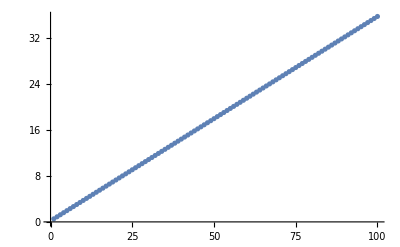

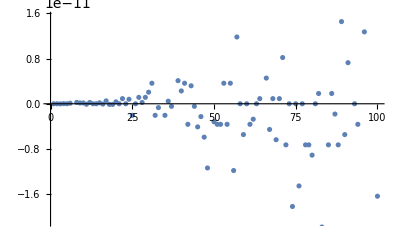

```mathematica
ListPlot[{Im/@wf1list7}]
ListPlot[{Re/@wf1list7}]
```

```mathematica
ampReg=(amp2-reg1)* Exp[-I zb-0.001Abs[zb]];
```

```mathematica
ampUnReg=(amp2)* Exp[-I zb-0.001Abs[zb]];
ampNumUnReg=ampUnReg/.ω->1//Expand;
```

```mathematica
Monitor[wf1list50=Table[NIntegrate[ampNumUnReg,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

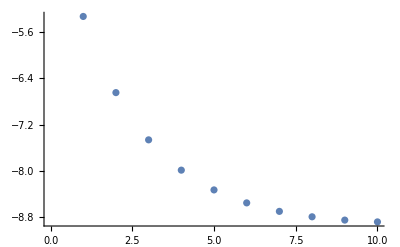

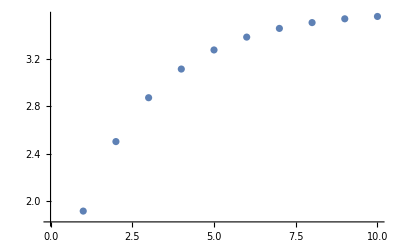

```mathematica
ListPlot[{Im/@wf1list50}]
ListPlot[{Re/@wf1list50}]
```

```mathematica
ampNumReg=ampUnReg/.ω->1//Expand;
```

```mathematica
NIntegrate[ampNumReg,{zv,0,40},{zb,-2 π-π,2 π+π+zv},Method->"LocalAdaptive"]
```

0.910798-2.97156 ⅈ

```mathematica
Monitor[wf1list5=Table[NIntegrate[ampNumReg,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
ampNumRegv=ampNumReg/.zv->40;
Monitor[wf1list5=Table[NIntegrate[ampNumRegv,{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

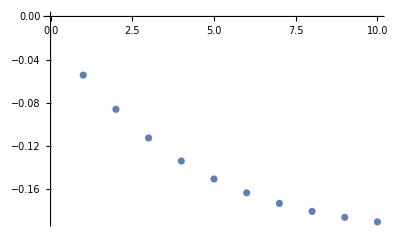

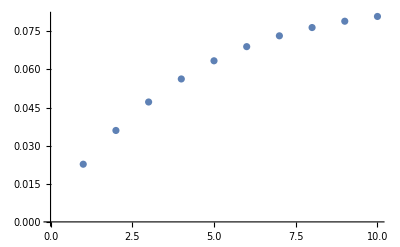

```mathematica
ListPlot[{Im/@wf1list5}]
ListPlot[{Re/@wf1list5}]
```

```mathematica
Monitor[wf1list5=Table[NIntegrate[ampNumReg/.zv->40,{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

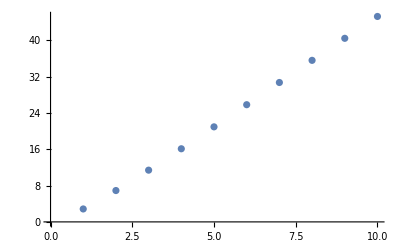

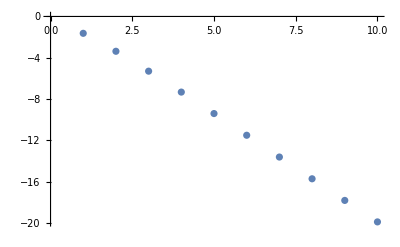

```mathematica
ListPlot[{Im/@wf1list5}]
ListPlot[{Re/@wf1list5}]
```

```mathematica
Monitor[wf1list6=Table[NIntegrate[ampNumUnReg,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
ListPlot[{Im/@wf1list6}]
ListPlot[{Re/@wf1list6}]
```

-Graphics-

-Graphics-

### Regularized Test zv finite

```mathematica
ampReg=(amp2-(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 ω (zv+1)))* Exp[-I zb-0.001Abs[zb]];
```

```mathematica
ampNumReg=ampReg/.ω->1;
```

```mathematica
Monitor[wf1listzv1=Table[NIntegrate[ampNumReg,{zv,0,ii*100},{zb,-20 π-π,20 π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

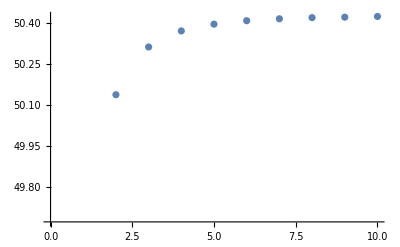

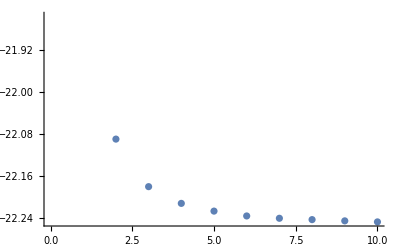

```mathematica
ListPlot[{Im/@wf1listzv1}]
ListPlot[{Re/@wf1listzv1}]
```

```mathematica
Monitor[wf1listzv1=Table[NIntegrate[ampNumReg,{zv,0,ii*10},{zb,-20 π-π,20 π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

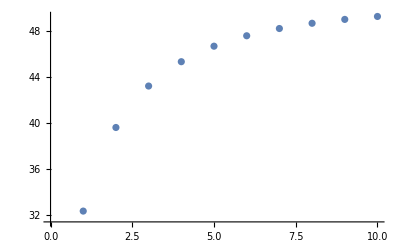

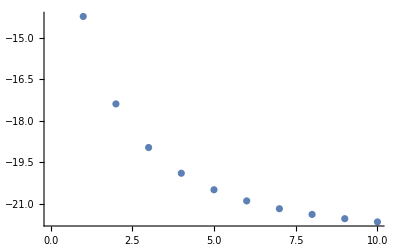

```mathematica
ListPlot[{Im/@wf1listzv1}]
ListPlot[{Re/@wf1listzv1}]
```

```mathematica
NIntegrate[ampNumReg,{zv,0,1000},{zb,-2*0 π-π,2*0 π+π},Method->"LocalAdaptive"]
```

-0.285564-0.301724 ⅈ

```mathematica
NIntegrate[ampNumReg,{zv,0,1000},{zb,-100* π-π,100* π+π},Method->"LocalAdaptive"]
```

$Aborted

```mathematica
Monitor[wf1list5=Table[NIntegrate[ampNumReg,{zv,0,1000},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

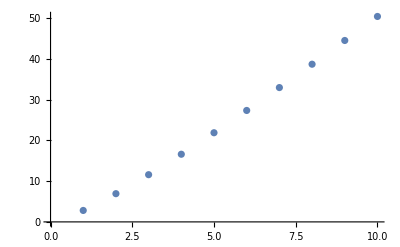

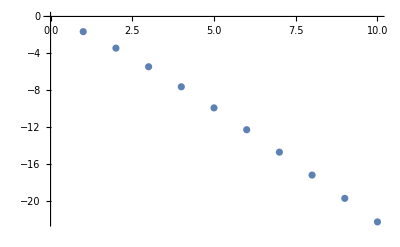

```mathematica
ListPlot[{Im/@wf1list5}]
ListPlot[{Re/@wf1list5}]
```

```mathematica
Monitor[wf1list6=Table[NIntegrate[ampNumReg,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
ListPlot[{Im/@wf1list5}]
ListPlot[{Re/@wf1list5}]
```

-Graphics-

-Graphics-

### Regularized2

```mathematica
reg1=Series[(amp2),{zv,∞,1}]//Normal;
```

```mathematica
reg1=reg1/.zv->zv+1;
```

```mathematica
reg1
```

(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 (1+zv) ω)

```mathematica
wf1list7=Table[NIntegrate[reg1/.ω->1,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,100}]
```

{0.+0.532802 ⅈ,0.+0.888004 ⅈ,-1.77636×10^-14+1.24321 ⅈ,2.4869×10^-14+1.59841 ⅈ,0.+1.95361 ⅈ,9.9476×10^-14+2.30881 ⅈ,-2.51892×10^-9+2.66401 ⅈ,2.41585×10^-13+3.01921 ⅈ,1.42109×10^-13+3.37442 ⅈ,1.42109×10^-13+3.72962 ⅈ,-8.52651×10^-14+4.08482 ⅈ,2.27374×10^-13+4.44002 ⅈ,0.+4.79522 ⅈ,0.+5.15042 ⅈ,1.7053×10^-13+5.50562 ⅈ,-5.68434×10^-14+5.86083 ⅈ,5.11591×10^-13+6.21603 ⅈ,-1.13687×10^-13+6.57123 ⅈ,-1.13687×10^-13+6.92643 ⅈ,3.41061×10^-13+7.28163 ⅈ,0.+7.63683 ⅈ,9.09495×10^-13+7.99204 ⅈ,0.+8.34724 ⅈ,7.95808×10^-13+8.70244 ⅈ,-2.04636×10^-12+9.05764 ⅈ,0.+9.41284 ⅈ,1.13687×10^-12+9.76804 ⅈ,2.27374×10^-13+10.1232 ⅈ,1.13687×10^-12+10.4784 ⅈ,2.04636×10^-12+10.8336 ⅈ,3.63798×10^-12+11.1889 ⅈ,-2.04636×10^-12+11.5441 ⅈ,-6.82121×10^-13+11.8993 ⅈ,-4.48745×10^-9+12.2545 ⅈ,-2.04636×10^-12+12.6097 ⅈ,4.54747×10^-13+12.9649 ⅈ,-4.54747×10^-13+13.3201 ⅈ,-3.13412×10^-9+13.6753 ⅈ,4.09273×10^-12+14.0305 ⅈ,2.27374×10^-12+14.3857 ⅈ,3.63798×10^-12+14.7409 ⅈ,-3.63798×10^-12+15.0961 ⅈ,3.18323×10^-12+15.4513 ⅈ,-4.54747×10^-13+15.8065 ⅈ,-4.09273×10^-12+16.1617 ⅈ,-2.27374×10^-12+16.5169 ⅈ,-5.91172×10^-12+16.8721 ⅈ,-1.13687×10^-11+17.2273 ⅈ,-5.08908×10^-9+17.5825 ⅈ,-3.18323×10^-12+17.9377 ⅈ,-3.63798×10^-12+18.2929 ⅈ,-3.63798×10^-12+18.6481 ⅈ,3.63798×10^-12+19.0033 ⅈ,-3.63798×10^-12+19.3585 ⅈ,3.63798×10^-12+19.7137 ⅈ,-1.18234×10^-11+20.0689 ⅈ,1.18234×10^-11+20.4241 ⅈ,0.+20.7793 ⅈ,-5.45697×10^-12+21.1345 ⅈ,0.+21.4897 ⅈ,-3.63798×10^-12+21.8449 ⅈ,-2.72848×10^-12+22.2001 ⅈ,0.+22.5553 ⅈ,9.09495×10^-13+22.9105 ⅈ,-8.99399×10^-9+23.2657 ⅈ,4.54747×10^-12+23.6209 ⅈ,-4.54747×10^-12+23.9761 ⅈ,9.09495×10^-13+24.3313 ⅈ,-6.36646×10^-12+24.6865 ⅈ,9.09495×10^-13+25.0417 ⅈ,8.18545×10^-12+25.3969 ⅈ,-7.27596×10^-12+25.7521 ⅈ,0.+26.1073 ⅈ,-1.81899×10^-11+26.4625 ⅈ,0.+26.8177 ⅈ,-1.45519×10^-11+27.1729 ⅈ,0.+27.5281 ⅈ,-7.27596×10^-12+27.8833 ⅈ,-7.27596×10^-12+28.2385 ⅈ,-9.09495×10^-12+28.5937 ⅈ,0.+28.9489 ⅈ,1.81899×10^-12+29.3041 ⅈ,-2.18279×10^-11+29.6593 ⅈ,-8.94579×10^-9+30.0145 ⅈ,-7.27596×10^-12+30.3697 ⅈ,1.81899×10^-12+30.7249 ⅈ,-1.81899×10^-12+31.0801 ⅈ,-7.27596×10^-12+31.4353 ⅈ,1.45519×10^-11+31.7905 ⅈ,-5.45697×10^-12+32.1457 ⅈ,7.27596×10^-12+32.5009 ⅈ,-2.36469×10^-11+32.8561 ⅈ,0.+33.2113 ⅈ,-3.63798×10^-12+33.5666 ⅈ,-4.00178×10^-11+33.9218 ⅈ,1.27329×10^-11+34.277 ⅈ,4.36557×10^-11+34.6322 ⅈ,-6.36646×10^-11+34.9874 ⅈ,1.81899×10^-11+35.3426 ⅈ,-1.63709×10^-11+35.6978 ⅈ}

```mathematica
ListPlot[{Im/@wf1list7}]
ListPlot[{Re/@wf1list7}]
```

-Graphics-

-Graphics-

```mathematica
ampReg=(amp2-reg1)* Exp[-I zb-0.001Abs[zb]];
```

```mathematica
ampUnReg=(amp2)* Exp[-I zb-0.001Abs[zb]];
ampNumUnReg=ampUnReg/.ω->1//Expand;
```

```mathematica
Monitor[wf1list50=Table[NIntegrate[ampNumUnReg,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
ListPlot[{Im/@wf1list50}]
ListPlot[{Re/@wf1list50}]
```

-Graphics-

-Graphics-

```mathematica
ampNumReg=ampUnReg/.ω->1//Expand;
```

```mathematica
NIntegrate[ampNumReg,{zv,0,40},{zb,-2 π-π,2 π+π+zv},Method->"LocalAdaptive"]
```

0.910798-2.97156 ⅈ

```mathematica
Monitor[wf1list5=Table[NIntegrate[ampNumReg,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
ampNumRegv=ampNumReg/.zv->40;
Monitor[wf1list5=Table[NIntegrate[ampNumRegv,{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
ListPlot[{Im/@wf1list5}]
ListPlot[{Re/@wf1list5}]
```

-Graphics-

-Graphics-

```mathematica
Monitor[wf1list5=Table[NIntegrate[ampNumReg/.zv->40,{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

```mathematica
ListPlot[{Im/@wf1list5}]
ListPlot[{Re/@wf1list5}]
```

-Graphics-

-Graphics-

```mathematica
Monitor[wf1list6=Table[NIntegrate[ampNumUnReg,{zv,0,40},{zb,-2ii π-π,2ii π+π},Method->"LocalAdaptive"],{ii,10}];,ii]
```

```mathematica
ListPlot[{Im/@wf1list6}]
ListPlot[{Re/@wf1list6}]
```

-Graphics-

-Graphics-

### Plot waveform

```mathematica
reg1jhome=reg1/.(zv+1)->zv+ω
```

(9 (76 √2 zb+19 ⅈ √6 zb+4 ⅈ √3 ω))/(8192 ω (zv+ω))

```mathematica
ampReg=(amp2-reg1jhome)* Exp[-I zb-0.001Abs[zb]];
```

```mathematica
Monitor[wf1listzv1=Table[NIntegrate[ampReg,{zv,0,100},{zb,-20 π-π,20 π+π},Method->"LocalAdaptive"],{ω,0.6,2.2,0.1}];,ω]
```

```mathematica
wfIm=Table[{0.5+0.1*ii,Im[wf1listzv1[[ii]]]},{ii,Length@wf1listzv1}];
wfRe=Table[{0.5+0.1*ii,Re[wf1listzv1[[ii]]]},{ii,Length@wf1listzv1}];
```

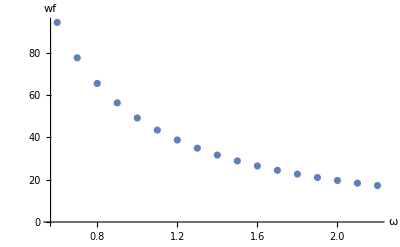

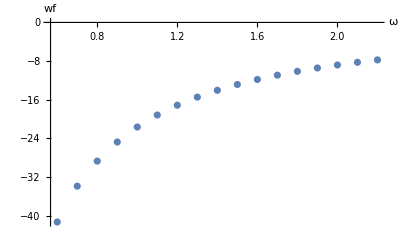

```mathematica
ListPlot[wfIm,AxesLabel->{ω,wf}]
ListPlot[wfRe,AxesLabel->{ω,wf}]
```